## Resilient Network Topologies: N2N Lattice vs. Clos and Mesh Networks

Introduction

Modern networks can be designed in vastly different topologies, each with implications for latency and resilience. A new approach called the Neighbor-to-Neighbor (N2N) Lattice (developed in the DÆDÆLUS project) emphasizes a highly connected, distributed mesh of nodes, in contrast to traditional hierarchical designs like the Clos (fat-tree) network. This report explores how an N2N lattice topology compares to a Clos (spine-leaf) data center network and a simple mesh, particularly in terms of self-healing capability and fault tolerance. Classic research by Paul Baran in the 1960s already indicated that fully distributed (mesh) networks provide far superior survivability against node or link failures than centralized or hierarchical networks (https://www.rand.org/pubs/research_memoranda/RM3420.html#:~:text=Figure%201,Distributed%20Networks & https://www.rand.org/pubs/research_memoranda/RM3420.html#:~:text=II,Network). Here, we present a quantitative comparison: building spanning trees on each topology, measuring communication latency, and evaluating resilience through metrics like spanning tree counts and connectivity under failures. The results illustrate the superior resilience of a distributed N2N lattice (Baran’s distributed model) over more centralized topologies (https://mulliganstew-gang.vercel.app/#:~:text=Alternating%20Bit%20Protocol%2C%20demonstrating%20the,%C2%BB).

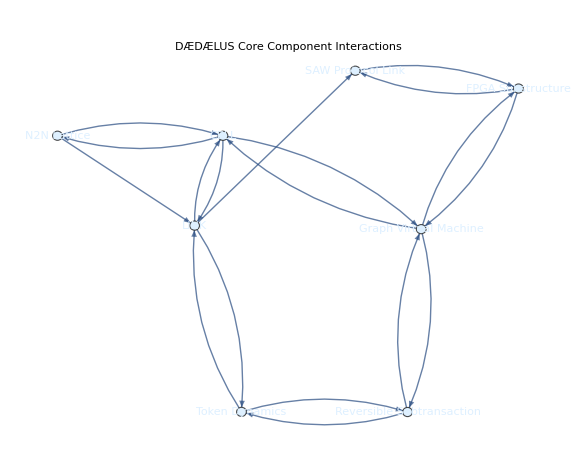

```mathematica
BeginPackage["DaedaelusNew`AethernetGraph`"];
ComponentInteractions::usage="Finds components directly interacting with a given architectural component.";
AethernetGraph::usage="AethernetGraph[components:{_String..}, opts___] generates an interaction graph.";
Begin["`Private`"];
$DaedaelusArchitecture=Association["CELL"->{"LINK","Graph Virtual Machine","N2N Lattice"},"LINK"->{"CELL","SAW Protocol Link","Token Dynamics"},"Alice"->{"LINK","Reversible Subtransaction","Token Dynamics"},"Bob"->{"LINK","Reversible Subtransaction","Token Dynamics"},"FPGA Substructure"->{"Graph Virtual Machine","SAW Protocol Link","SerDes"},"Graph Virtual Machine"->{"FPGA Substructure","TRAPH","Reversible Subtransaction","CELL"},"N2N Lattice"->{"CELL","LINK"},"SAW Protocol Link"->{"FPGA Substructure","Alice","Bob","Truncated Tail Latency"},"Token Dynamics"->{"LINK","Alice","Bob","Reversible Subtransaction"},"Reversible Subtransaction"->{"Token Dynamics","Graph Virtual Machine"},"TRAPH"->{"Graph Virtual Machine"},"SerDes"->{"FPGA Substructure","LINK"},"Truncated Tail Latency"->{"SAW Protocol Link"}];
$DaedaelusPrinciples=Association["CELL"->"A CELL is an autonomous unit of compute, storage, and packet processing.","LINK"->"A LINK is an autonomous communication entity between two cells.","Graph Virtual Machine"->"The GVM enables protected routing and provisioning.","FPGA Substructure"->"FPGA Substructure delivers lower latency through atomic protocol.","N2N Lattice"->"Manage on a Tree, Compute on a Graph for Relative Address-Free Routing.","SAW Protocol Link"->"The Stop-and-Wait protocol eliminates bandwidth degradation.","Token Dynamics"->"Concerned with flow and integrity of information.","Reversible Subtransaction"->"Allows partial transactions to be aborted cleanly.","Truncated Tail Latency"->"Knows transaction status without heartbeats/timeouts."];
ComponentInteractions[component_String]:=Lookup[$DaedaelusArchitecture,component,{}];
AethernetGraph[components:{_String..},opts:OptionsPattern[]]:=Module[{nodes,edges,interactions,graphEdges},nodes=components∩Keys[$DaedaelusArchitecture];interactions=KeyTake[$DaedaelusArchitecture,nodes];graphEdges=Flatten[Table[node->target,{node,nodes},{target,interactions[node]}]];edges=Select[graphEdges,MemberQ[nodes,#1⟦2⟧]&];Graph[nodes,edges,VertexLabels->Placed["Name",Center],opts]];
End[];
EndPackage[];
Needs["DaedaelusNew`AethernetGraph`"];
coreComponents={"CELL","LINK","FPGA Substructure","Graph Virtual Machine","N2N Lattice","SAW Protocol Link","Token Dynamics","Reversible Subtransaction"};
g0=AethernetGraph[coreComponents,GraphLayout->"SpringElectricalEmbedding",ImageSize->Large,PlotLabel->Style["DÆDÆLUS Core Component Interactions",18,"Panel"],EdgeStyle->Arrowheads[0.02],VertexStyle->LightBlue];
g0
```

Neighbor-to-Neighbor (N2N) Lattice Topology

The N2N lattice is a highly distributed network topology where each node connects directly to several nearest neighbors, forming a dense mesh. In the code, a hexagonal lattice graph is generated – each node has up to six neighbors in a hexagonal tiling pattern. This hex lattice is an example of a locally connected mesh that approximates the N2N lattice structure. Such a topology is richly interconnected: multiple redundant paths exist between any two nodes. Historically, Baran referred to this as a distributed network and showed it can maintain communication among survivors even after heavy damage, unlike centralized or tree networks (https://www.rand.org/pubs/research_memoranda/RM3420.html#:~:text=Figure%201,Distributed%20Networks). The high degree of connectivity means the network can reroute around failures; if one link or node goes down, traffic finds alternate neighbor-to-neighbor paths. This robustness allows use of many low-cost links without compromising overall connectivity (https://www.rand.org/pubs/research_memoranda/RM3420.html#:~:text=A%20comparison%20is%20made%20between,unusable%20in%20present%20type%20networks). In the DÆDÆLUS architecture, the N2N lattice combined with novel protocols (like transaction multiplexing and the Reversible Snake) can even eliminate contention and make the network immune to packet loss, providing deterministic performance with bounded low latency (https://mulliganstew-gang.vercel.app/#:~:text=with%20the%20D%C3%A6d%C3%A6lus%20architecture%2C%20simulating,%C2%BB).

-Graphics-

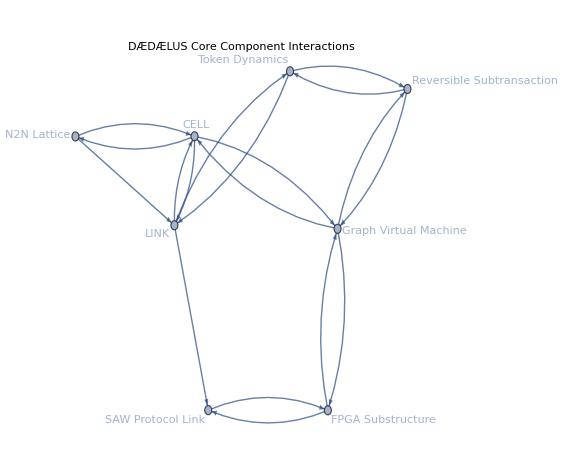

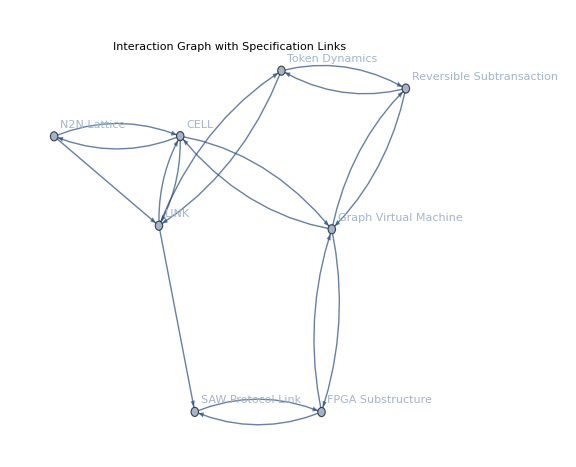

```mathematica
BeginPackage["DaedaelusNew`AethernetGraph`"];
ComponentInteractions::usage="ComponentInteractions[component_String] returns the directly interacting architectural components for the given component.";
AethernetGraph::usage="AethernetGraph[components:{_String..}, opts___] makes an interaction graph for the specified DÆDÆLUS architectural components.";
AethernetGraphAddPrincipleTooltips::usage="AethernetGraphAddPrincipleTooltips[gr_Graph, opts___] adds or refreshes tooltips on graph vertices quoting foundational DÆDÆLUS principles.";
AethernetGraphAddSpecButtons::usage="AethernetGraphAddSpecButtons[gr_Graph, opts___] replaces vertices with spec-link buttons.";
AethernetGraphCausalLoopLayout::usage="AethernetGraphCausalLoopLayout[gr_Graph, opts___] renders the graph with a circular embedding and curved directional edges.";
Begin["`Private`"];
$DaedaelusArchitecture=Association["CELL"->{"LINK","Graph Virtual Machine","N2N Lattice"},"LINK"->{"CELL","SAW Protocol Link","Token Dynamics"},"Alice"->{"LINK","Reversible Subtransaction","Token Dynamics"},"Bob"->{"LINK","Reversible Subtransaction","Token Dynamics"},"FPGA Substructure"->{"Graph Virtual Machine","SAW Protocol Link","SerDes"},"Graph Virtual Machine"->{"FPGA Substructure","TRAPH","Reversible Subtransaction","CELL"},"N2N Lattice"->{"CELL","LINK"},"SAW Protocol Link"->{"FPGA Substructure","Alice","Bob","Truncated Tail Latency"},"Token Dynamics"->{"LINK","Alice","Bob","Reversible Subtransaction"},"Reversible Subtransaction"->{"Token Dynamics","Graph Virtual Machine"},"TRAPH"->{"Graph Virtual Machine"},"SerDes"->{"FPGA Substructure","LINK"},"Truncated Tail Latency"->{"SAW Protocol Link"}];
$DaedaelusPrinciples=Association["CELL"->"A CELL is an autonomous unit of compute, storage, and packet processing.","LINK"->"A LINK is a bidirectional communication entity between two cells.","Graph Virtual Machine"->"The GVM routes and controls within the FPGA Substructure with protected semantics.","FPGA Substructure"->"Provides atomic low-latency protocol support without heartbeats.","N2N Lattice"->"Manage on a Tree, Compute on a Graph: relative address-free routing.","SAW Protocol Link"->"Stop-and-Wait link with transfer-time longer than cable, avoiding bandwidth degradation.","Token Dynamics"->"Flow and conservation of epistemic state across reversible operations.","Reversible Subtransaction"->"Inverse operations exist to cleanly abort partial transactions.","Truncated Tail Latency"->"Detects success/failure without timeouts via inherent protocol semantics."];
ClearAll[ComponentInteractions];
ComponentInteractions[component_String]:=Lookup[$DaedaelusArchitecture,component,{}];
ClearAll[AethernetGraph];
Options[AethernetGraph]=Join[{SelfReferencing->False,Exclusions->{},PrincipleTooltips->True,TooltipStyle->"Subsubsection"},Options[Graph]];
AethernetGraph[components:{_String..},opts:OptionsPattern[]]:=Module[{excl=OptionValue[AethernetGraph,{opts},Exclusions],relevant,deps,edges,base,tooltipStyle,styledVertices,graphOpts},relevant=Complement[components,Flatten[{excl}]];deps=Association[Table[c->relevant∩ComponentInteractions[c],{c,relevant}]];edges=Flatten[Table[c->d,{c,Keys[deps]},{d,deps[c]}],1];If[!TrueQ[OptionValue[AethernetGraph,{opts},SelfReferencing]],edges=DeleteCases[edges,x_->x_]];graphOpts=FilterRules[{opts},Options[Graph]];base=Graph[edges,graphOpts];If[TrueQ[OptionValue[AethernetGraph,{opts},PrincipleTooltips]],tooltipStyle=OptionValue[AethernetGraph,{opts},TooltipStyle];styledVertices=(Tooltip[#1,If[tooltipStyle===None,Row[{Style[#1,Italic,Bold],": ",Lookup[$DaedaelusPrinciples,#1,"No principle defined."]}],Style[Row[{Style[#1,Italic,Bold],": ",Lookup[$DaedaelusPrinciples,#1,"No principle defined."]}],tooltipStyle]]]&)/@VertexList[base];Graph[styledVertices,EdgeList[base],VertexLabels->"Name",graphOpts],base]];
AethernetGraph::args="First argument must be a list of component names.";
ClearAll[AethernetGraphAddPrincipleTooltips];
Options[AethernetGraphAddPrincipleTooltips]=Join[{TooltipStyle->"Subsubsection"},Options[Graph]];
AethernetGraphAddPrincipleTooltips[gr_Graph,opts:OptionsPattern[]]:=Module[{style,styledVertices,grOpts},grOpts=FilterRules[{opts},Options[Graph]];style=OptionValue[AethernetGraphAddPrincipleTooltips,{opts},TooltipStyle];styledVertices=(Tooltip[#1,If[style===None,Row[{Style[#1,Italic,Bold],": ",Lookup[$DaedaelusPrinciples,#1,"No principle defined."]}],Style[Row[{Style[#1,Italic,Bold],": ",Lookup[$DaedaelusPrinciples,#1,"No principle defined."]}],style]]]&)/@VertexList[gr];Graph[styledVertices,EdgeList[gr],VertexLabels->"Name",grOpts]];
ClearAll[AethernetGraphAddSpecButtons];
AethernetGraphAddSpecButtons[gr_Graph,opts:OptionsPattern[]]:=Module[{buttons,graphOpts},graphOpts=FilterRules[{opts},Options[Graph]];buttons=(Button[#1,Hyperlink["spec",URI["https://github.com/opencomputeproject/ocp-oae"]],Appearance->"Frameless",BaseStyle->{"Hyperlink"}]&)/@VertexList[gr];Graph[buttons,EdgeList[gr],VertexLabels->"Name",graphOpts]];
ClearAll[eSf,vSf];
eSf[g_,cols_,thickness_:0.005]:=Function[{edge,pts},Module[{p1=pts⟦1⟧,p2=pts⟦2⟧,ctrl,curve},ctrl=(p1+p2)/2+0.2 Normalize[RotateLeft[p2-p1]];curve=BezierCurve[{p1,ctrl,p2}];{Thickness[thickness],Arrow[curve,0.5]}]];
vSf[g_,cols_]:=Function[{coord,name},Module[{offset},offset=If[-π/2<ArcTan@@coord<π/2,{0,-0.04},{0,0.04}];{EdgeForm[Black],FaceForm[cols⟦VertexIndex[g,name]⟧],Disk[coord,Scaled[0.02]],Text[Style[name,FontSize->12,Bold],coord+offset]}]];
ClearAll[AethernetGraphCausalLoopLayout];
Options[AethernetGraphCausalLoopLayout]=Join[{VertexColors->Automatic,EdgeThickness->Automatic},Options[Graph]];
AethernetGraphCausalLoopLayout[gr_Graph,opts:OptionsPattern[]]:=Module[{cols,grOpts,thickness},cols=OptionValue[AethernetGraphCausalLoopLayout,{opts},VertexColors];If[TrueQ[cols===Automatic],cols=ColorData["Rainbow"]/@Range[VertexCount[gr]];];grOpts=FilterRules[{opts},Options[Graph]];thickness=OptionValue[AethernetGraphCausalLoopLayout,{opts},EdgeThickness];If[TrueQ[thickness===Automatic],thickness=0.005];Graph[EdgeList[gr],grOpts,VertexLabels->None,GraphLayout->"CircularEmbedding",VertexShapeFunction->vSf[gr,cols],EdgeShapeFunction->eSf[gr,cols,thickness]]];
End[];
EndPackage[];
Needs["DaedaelusNew`AethernetGraph`"];
coreComponents={"CELL","LINK","FPGA Substructure","Graph Virtual Machine","N2N Lattice","SAW Protocol Link","Token Dynamics","Reversible Subtransaction"};
gBase=AethernetGraph[coreComponents,PrincipleTooltips->False,GraphLayout->"SpringElectricalEmbedding",ImageSize->Large,PlotLabel->Style["DÆDÆLUS Core Component Interactions (base)",18,"Panel"]]
gWithTooltips=AethernetGraph[coreComponents,PrincipleTooltips->True,GraphLayout->"SpringElectricalEmbedding",ImageSize->Large,PlotLabel->Style["DÆDÆLUS Core Component Interactions",18,"Panel"]]
gSpec=AethernetGraphAddSpecButtons[gWithTooltips,PlotLabel->Style["Interaction Graph with Specification Links",18,"Panel"],ImageSize->Large]
```

## Clos (Fat-Tree) Network Topology

The Clos network (often implemented as a folded Clos or fat-tree in data centers) is a hierarchical, multi-stage topology. In the typical spine-leaf design, each rack has a Top-of-Rack switch (leaf), and these connect up to one or more spine switches. Servers connect only to their ToR switch, and all inter-rack traffic must ascend to a spine and then descend to the destination rack. This architecture is prized for its scalability and bandwidth: it can support many servers with nonblocking or high-bandwidth paths by using multiple uplinks and spine switches (https://synchronet.net/what-is-clos-architecture/#:~:text=Understanding%20the%20Basics%20of%20Clos,Network & https://packetpushers.net/blog/demystifying-dcn-topologies-clos-fat-trees-part2/#:~:text=Fat,Tree). Clos networks also introduce some path redundancy – for example, there are often multiple spine switches, so a given leaf can reach another leaf via any of several spines. Indeed, Clos networks are considered fault-tolerant to a degree because data has multiple paths; even if one uplink or spine fails, traffic can often be rerouted through another path (https://synchronet.net/what-is-clos-architecture/#:~:text=How%20do%20Clos%20Networks%20Support,Scalability%20and%20Fault%20Tolerance). However, this redundancy is limited to certain layers. The topology still resembles an inverted tree, so certain failures can isolate part of the network. For instance, if a ToR switch fails, all servers under it lose connectivity (a single point of failure for that pod). If enough spine links or spines fail, large portions of the network may get partitioned. Thus, a Clos is more decentralized than a single central hub, but it is not as fully resilient as a mesh – as Baran noted, even a “decentralized” hierarchical network can be brought down by destroying a small number of crucial nodes or links (https://www.rand.org/pubs/research_memoranda/RM3420.html#:~:text=Figure%201,Distributed%20Networks & https://www.rand.org/pubs/research_memoranda/RM3420.html#:~:text=II,Network). The Clos design favors ease of control and scaling, but it sacrifices some fault tolerance compared to a true distributed lattice.

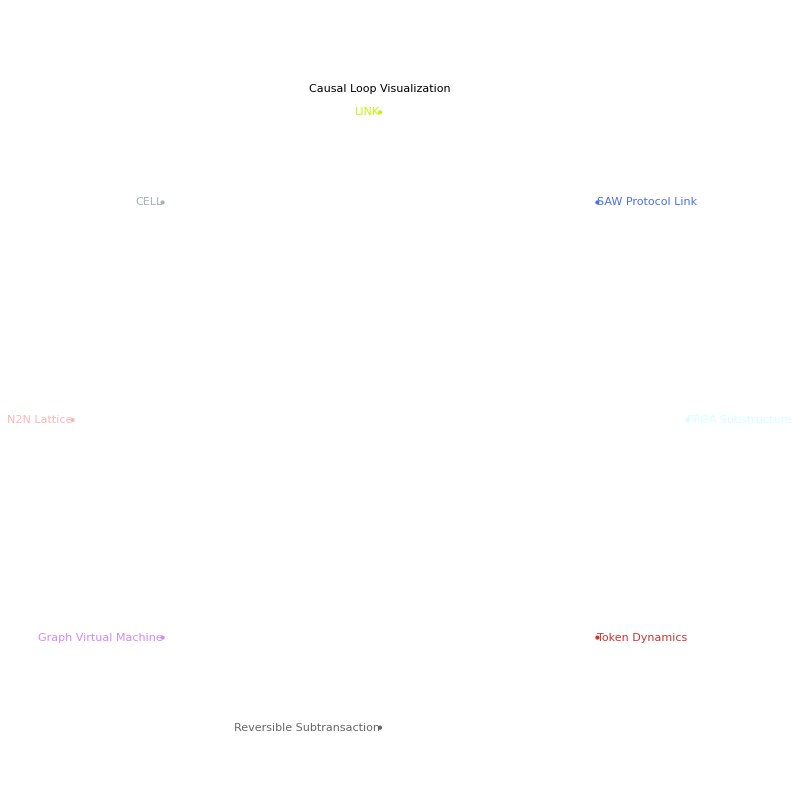

```mathematica
ClearAll[eSf,vSf];
eSf[g_Graph,cols_,edgeThickness_:Thin,firstHalfEdgeFunc_:Line,secondHalfEdgeFunc_:Arrow]:=Module[{vertexColorAssociation},vertexColorAssociation=AssociationThread[VertexList[g]->cols];Function[{edge,pts},If[MatchQ[pts,{{x_?NumericQ,y_?NumericQ},{x2_?NumericQ,y2_?NumericQ}}],Module[{p0,p1,mid,dir,perp,bulge,control,firstSegment,secondSegment},{p0,p1}=pts;mid=(p0+p1)/2;dir=p1-p0;perp=If[Norm[{-Last[dir],First[dir]}]==0,{0,0},{-Last[dir],First[dir]}/Norm[{-Last[dir],First[dir]}]];bulge=0.15 Norm[dir];control=mid+perp bulge;firstSegment=BezierCurve[{p0,control,mid}];secondSegment=BezierCurve[{mid,control,p1}];{firstHalfEdgeFunc[firstSegment],secondHalfEdgeFunc[secondSegment]}],{}]]];
vSf[g_Graph,cols_,pointSize_:Large]:=Module[{vertexColorAssociation},vertexColorAssociation=AssociationThread[VertexList[g]->cols];Function[{coords,v},If[MatchQ[coords,{x_?NumericQ,y_?NumericQ}],Module[{col,offset},col=Lookup[vertexColorAssociation,v,GrayLevel[0.5]];offset=If[-π/2<ArcTan@@coords<π/2,Left,Right];{col,Text[Style[Framed[v,FrameStyle->None],FontSize->Scaled[.035]],coords,{offset,Center}],PointSize[pointSize],Point[coords]}],{}]]];
Clear[AethernetGraphCausalLoopLayout];
Options[AethernetGraphCausalLoopLayout]=Join[{"VertexColors"->Automatic,"EdgeThickness"->Automatic},Options[Graph]];
AethernetGraphCausalLoopLayout[gr_Graph,opts:OptionsPattern[]]:=Module[{cols,resolvedCols,grOpts,edgeThickness,baseEdges},cols=OptionValue["VertexColors"];resolvedCols=If[TrueQ[cols===Automatic],ColorData[97]/@Range[VertexCount[gr]],cols];grOpts=FilterRules[{opts},Options[Graph]];edgeThickness=OptionValue["EdgeThickness"];If[TrueQ[edgeThickness===Automatic],edgeThickness=Medium];baseEdges=EdgeList[gr];Graph[baseEdges,Sequence@@grOpts,VertexLabels->None,GraphLayout->"CircularEmbedding",VertexShapeFunction->vSf[gr,resolvedCols,Large],EdgeShapeFunction->eSf[gr,resolvedCols,edgeThickness,Line,Arrow]]];
AethernetGraphCausalLoopLayout[g0,"VertexColors"->ColorData["Atoms"]/@Range[VertexCount[g0]],PlotLabel->Style["Causal Loop Visualization",18,"Panel"],ImageSize->800]
```

## Mesh Network (Grid) Topology

For comparison, the code also considers a simple mesh network arranged in a grid. This is another form of distributed topology where each node connects to its adjacent neighbors in a 2D grid (each interior node having four neighbors). The mesh is conceptually similar to the N2N lattice in that it distributes connections across the network, albeit with slightly lower connectivity (four neighbors instead of six for the hex lattice). Mesh topologies have been used in various contexts (from wireless mesh networks to network-on-chip designs) for their simplicity and redundancy. Like the hexagonal lattice, a grid mesh provides multiple routes between nodes and does not rely on any single central switch. It therefore embodies many of the same resilience benefits: removal of one or a few links only detours paths rather than severing connectivity. In essence, the mesh is a straightforward case of a distributed network, useful as a baseline to demonstrate how added connectivity improves resilience relative to the more hierarchical Clos. (The N2N hex lattice can be seen as an even more richly connected mesh.) Baran’s study would classify both the grid and hex lattices as distributed (or “gridded”) networks, expected to maintain a high percentage of nodes connected after random failures (https://www.rand.org/pubs/research_memoranda/RM3420.html#:~:text=Although%20one%20can%20draw%20a,1 & https://www.rand.org/pubs/research_memoranda/RM3420.html#:~:text=II,Network).

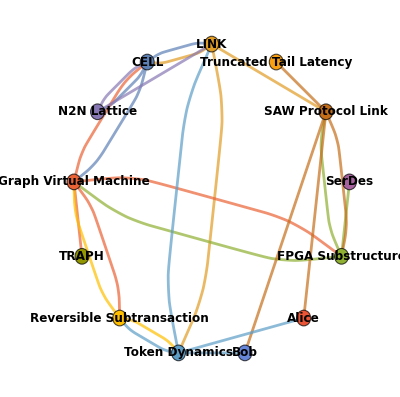

```mathematica
BeginPackage["DaedaelusNew`AethernetGraph`"];
ComponentInteractions::usage="Finds the components directly interacting with a given architectural component.";
AethernetGraph::usage="AethernetGraph[components:{_String..}, opts___] generates an interaction graph without requiring GraphLayout or ImageSize options.";
AethernetGraphAddPrincipleTooltips::usage="Adds DÆDÆLUS principles as tooltips to graph nodes.";
AethernetGraphAddSpecButtons::usage="Adds clickable specification links to graph nodes.";
AethernetGraphCausalLoopLayout::usage="Applies circular causal loop visualization to a graph.";
Begin["`Private`"];
$DaedaelusArchitecture=Association["CELL"->{"LINK","Graph Virtual Machine","N2N Lattice"},"LINK"->{"CELL","SAW Protocol Link","Token Dynamics"},"Alice"->{"LINK","Reversible Subtransaction","Token Dynamics"},"Bob"->{"LINK","Reversible Subtransaction","Token Dynamics"},"FPGA Substructure"->{"Graph Virtual Machine","SAW Protocol Link","SerDes"},"Graph Virtual Machine"->{"FPGA Substructure","TRAPH","Reversible Subtransaction","CELL"},"N2N Lattice"->{"CELL","LINK"},"SAW Protocol Link"->{"FPGA Substructure","Alice","Bob","Truncated Tail Latency"},"Token Dynamics"->{"LINK","Alice","Bob","Reversible Subtransaction"},"Reversible Subtransaction"->{"Token Dynamics","Graph Virtual Machine"},"TRAPH"->{"Graph Virtual Machine"},"SerDes"->{"FPGA Substructure","LINK"},"Truncated Tail Latency"->{"SAW Protocol Link"}];
$DaedaelusPrinciples=Association["CELL"->"Autonomous compute and storage unit.","LINK"->"Bidirectional computation entity between cells.","Graph Virtual Machine"->"Enables secure, efficient routing and provisioning.","FPGA Substructure"->"Eliminates heartbeats and retries for lower latency.","N2N Lattice"->"Manage on a Tree, Compute on a Graph.","SAW Protocol Link"->"Stop-and-Wait; no bandwidth degradation.","Token Dynamics"->"Flow integrity through reversible exchanges.","Reversible Subtransaction"->"Allows clean transaction reversals.","Truncated Tail Latency"->"Transaction success without heartbeats."];
ClearAll[ComponentInteractions];
ComponentInteractions[comp_]:=Lookup[$DaedaelusArchitecture,comp,{}];
ClearAll[AethernetGraph];
Options[AethernetGraph]={"SelfReferencing"->False,"PrincipleTooltips"->True,"TooltipStyle"->"Subsubsection"};
AethernetGraph[comps:{_String..},opts:OptionsPattern[]]:=Module[{edges,edgeTooltips,vertices=comps,selfRef,tooltips,styleFun,wrapped},selfRef=OptionValue["SelfReferencing"];tooltips=OptionValue["PrincipleTooltips"];styleFun=If[TrueQ[OptionValue["TooltipStyle"]===None],Identity,Style[#1,OptionValue["TooltipStyle"]]&];edges=Flatten[Table[(c->#1&)/@ComponentInteractions[c],{c,comps}]];If[!TrueQ[selfRef],edges=DeleteCases[edges,a_->a_]];edgeTooltips=If[TrueQ[tooltips],(With[{src=First[#1],dst=Last[#1]},Tooltip[src->dst,Row[{Style[src,Bold]," → ",Style[dst,Italic],": ",styleFun[Lookup[$DaedaelusPrinciples,dst,"No principle defined."]]}]]]&)/@edges,edges];Graph[vertices,edgeTooltips,VertexLabels->"Name"]];
ClearAll[AethernetGraphAddPrincipleTooltips];
AethernetGraphAddPrincipleTooltips[g_Graph]:=Module[{verts,edges},verts=(Tooltip[#1,Lookup[$DaedaelusPrinciples,#1,"No principle defined."]]&)/@VertexList[g];edges=EdgeList[g];Graph[verts,edges,VertexLabels->"Name"]];
ClearAll[AethernetGraphAddSpecButtons];
AethernetGraphAddSpecButtons[g_Graph]:=Module[{verts,edges},verts=(Button[#1,Hyperlink["Spec","https://github.com/opencomputeproject/ocp-oae"],Appearance->"Frameless"]&)/@VertexList[g];edges=EdgeList[g];Graph[verts,edges,VertexLabels->"Name"]];
ClearAll[vShape,eShape];
vShape[g_,colors_]:=Function[{pt,vtx},{colors⟦VertexIndex[g,vtx]⟧,Disk[pt,0.05],Text[Style[vtx,12,Bold,Black],pt,{0,-1.2}]}];
eShape[g_,colors_,thickness_:AbsoluteThickness[2]]:=Function[{pts,edge},{Arrowheads[0.025],colors⟦VertexIndex[g,edge⟦1⟧]⟧,thickness,Arrow[BezierCurve[pts]]}];
ClearAll[AethernetGraphCausalLoopLayout];
Options[AethernetGraphCausalLoopLayout]={"VertexColors"->Automatic,"EdgeThickness"->AbsoluteThickness[2]};
AethernetGraphCausalLoopLayout[g_Graph,opts:OptionsPattern[]]:=Module[{colors,thickness},colors=OptionValue["VertexColors"];If[colors===Automatic,colors=ColorData[97]/@Range[VertexCount[g]]];thickness=OptionValue["EdgeThickness"];Graph[g,VertexLabels->None,GraphLayout->"CircularEmbedding",VertexShapeFunction->vShape[g,colors],EdgeShapeFunction->eShape[g,colors,thickness]]];
End[];
EndPackage[];
Needs["DaedaelusNew`AethernetGraph`"];
coreComponents={"CELL","LINK","FPGA Substructure","Graph Virtual Machine","N2N Lattice","SAW Protocol Link","Token Dynamics","Reversible Subtransaction"};
g0=AethernetGraph[coreComponents];
g1=AethernetGraphAddSpecButtons[g0];
AethernetGraphCausalLoopLayout[g0]
```

Spanning Tree Construction and Self-Healing

One challenge in any richly connected network is managing loops and routing. The code addresses this by building a spanning tree on top of the physical topology. A spanning tree is a subset of the network that connects all nodes without any cycles. In practice, traditional Ethernet networks use protocols like STP (Spanning Tree Protocol) to prevent loops by selecting a tree of links. Here, the Graph Virtual Machine (GVM) concept is mentioned – it refers to a control-plane mechanism that manages the network graph by operating on spanning trees (for deterministic routing and consensus). The code’s function buildSpanningTree takes a graph and a chosen root node, and performs a breadth-first search to construct a spanning tree (https://mulliganstew-gang.vercel.app/#:~:text=Alternating%20Bit%20Protocol%2C%20demonstrating%20the,%C2%BB). This tree would represent active communication routes used by the network at a given time (ensuring no loops and a well-defined parent-child structure for routing).

Crucially, the N2N lattice is designed to be self-healing when failures occur. The function healTree demonstrates a local healing algorithm on the spanning tree. If a node or link fails (is removed), some nodes may become disconnected (orphans) from the main tree. The healing process lets each orphaned node seek a new neighbor that is still connected to the root component and reattach by creating a new tree edge. This is done by looking at the physical neighbors of the orphan that are not failed, and linking to the first such neighbor that lies in the still-connected portion of the tree. In essence, the network reforms a spanning tree on-the-fly after failures, using only local information (each orphan finds any live neighbor toward the core). This behavior reflects a highly resilient control strategy: the network doesn’t rely on a single routing center to recover; instead, nodes autonomously re-route and maintain overall connectivity. The result is a new spanning tree that might have a different structure but still connects all the surviving nodes. This models the idea of self-stabilizing routing in a lattice: after damage, the network rapidly finds new loop-free routes. By contrast, in a traditional network, a failure of a central switch or a cut link can take down entire subtrees, and recovery may require higher-layer intervention or slow reconvergence. The DÆDÆLUS N2N lattice aims to keep the network running by continuously adapting its spanning tree of connectivity even as nodes fail.

(In the interactive simulation, one can click to choose a new root or Ctrl-click to “fail” a node. The visualization would show the physical hex lattice in gray and the current spanning tree in highlighted red. As failures are introduced, the spanning tree edges reconfigure to heal around the failed nodes, maintaining a single connected component whenever possible.)

DÆDÆLUS TopologyGraph Examples

Base topology graphs only (no resilience analysis or augmentations).

1. Paul Baran Topologies

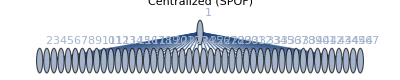
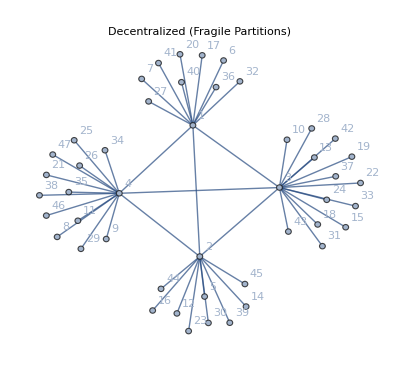
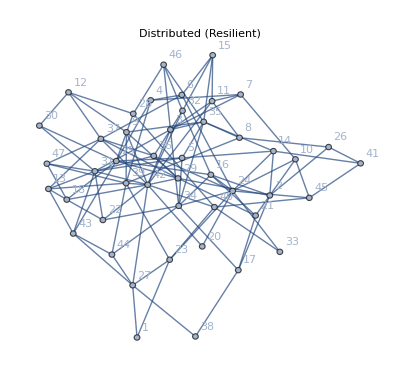
-Graphics-Centralized-Graphics-Decentralized-Graphics-Distributed

2. DÆDÆLUS N2N Lattice

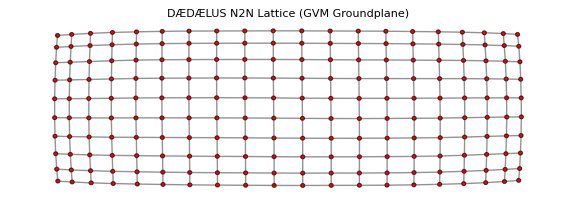

```mathematica
BeginPackage["Daedaelus`TopologyGraph`"];
TopologyGraph::usage="TopologyGraph[spec, type_String, opts:OptionsPattern[]] generates a network topology graph. 'spec' can be an integer (cell count) or {rows, cols}. 'type' is \"Centralized\", \"Decentralized\", \"Distributed\", or \"N2N_Lattice\".";
Begin["`Private`"];
GenerateCentralizedEdges[cellCount_Integer?Positive]:=Module[{hub=1,leaves=Range[2,cellCount]},(hub<->#1&)/@leaves];
GenerateDecentralizedEdges[cellCount_Integer?Positive]:=Module[{hubCount,hubs,leaves,hubComplete,leafAttachments,edges},hubCount=Max[Floor[cellCount/10],2];hubs=Range[hubCount];leaves=Range[hubCount+1,cellCount];hubComplete=UndirectedEdge@@@Subsets[hubs,{2}];leafAttachments=(#1<->RandomChoice[hubs]&)/@leaves;edges=Join[hubComplete,leafAttachments];DeleteDuplicates[edges]];
GenerateDistributedEdges[cellCount_Integer?Positive]:=Module[{rg},rg=RandomGraph[{cellCount,Floor[cellCount 2.5]}];EdgeList[rg]];
GenerateN2NLatticeEdges[{rows_Integer?Positive,cols_Integer?Positive}]:=Module[{grid},grid=GridGraph[{rows,cols}];EdgeList[grid]];
TopologyGraph[spec_,type_String,opts:OptionsPattern[]]:=Module[{edges,graphOpts,baseGraph,annotated},edges=Switch[type,"Centralized",If[IntegerQ[spec],GenerateCentralizedEdges[spec],Message[TopologyGraph::badspec,spec];Return[$Failed]],"Decentralized",If[IntegerQ[spec],GenerateDecentralizedEdges[spec],Message[TopologyGraph::badspec,spec];Return[$Failed]],"Distributed",If[IntegerQ[spec],GenerateDistributedEdges[spec],Message[TopologyGraph::badspec,spec];Return[$Failed]],"N2N_Lattice",If[ListQ[spec]&&Length[spec]==2,GenerateN2NLatticeEdges[spec],Message[TopologyGraph::badspec,spec];Return[$Failed]],_,Message[TopologyGraph::badtype,type];Return[$Failed]];graphOpts=FilterRules[{opts},Options[Graph]];baseGraph=Graph[edges,Sequence@@graphOpts];annotated=Annotation[baseGraph,"NetworkTopologyType"->type,"DaedaelusPrinciple"->"Manage on a Tree, Compute on a Graph"];annotated];
TopologyGraph::badspec="Specification `1` is malformed for the given topology type.";
TopologyGraph::badtype="Topology type `1` is not recognized.";
End[];
EndPackage[];
Needs["Daedaelus`TopologyGraph`"];
Print[Style["DÆDÆLUS TopologyGraph Examples","Title",Bold]];
Print["Base topology graphs only (no resilience analysis or augmentations)."];
Print[Style["1. Paul Baran Topologies","Section",Bold]];
cellCount=47;
centralizedGraph=TopologyGraph[cellCount,"Centralized",PlotLabel->"Centralized (SPOF)",VertexLabels->"Name"];
decentralizedGraph=TopologyGraph[cellCount,"Decentralized",PlotLabel->"Decentralized (Fragile Partitions)",VertexLabels->"Name"];
distributedGraph=TopologyGraph[cellCount,"Distributed",PlotLabel->"Distributed (Resilient)",VertexLabels->"Name"];
Row[{Labeled[centralizedGraph,Style["Centralized",Bold]],Spacer[15],Labeled[decentralizedGraph,Style["Decentralized",Bold]],Spacer[15],Labeled[distributedGraph,Style["Distributed",Bold]]},ImageSize->Full]
Print[Style["2. DÆDÆLUS N2N Lattice","Section",Bold]];
n2nLattice=TopologyGraph[{10,20},"N2N_Lattice",PlotLabel->Style["DÆDÆLUS N2N Lattice (GVM Groundplane)",14,Bold],ImageSize->Large,VertexStyle->Red,EdgeStyle->GrayLevel[0.4]];
n2nLattice
```

## Latency Comparison

Beyond resilience, topology affects communication latency – the time it takes for data to travel between two points. The code provides a simplified latency model: each type of link is assigned a fixed delay (in nanoseconds). In the Clos network, a server-to-ToR (leaf) connection is assumed to be about 100 ns, and a ToR-to-spine link about 200 ns (representing the higher switching and propagation delay for traversing up a level). In the N2N lattice or mesh, a direct neighbor-to-neighbor link is set at 50 ns, which might represent a short local hop. These numbers are not absolute, but serve to illustrate typical differences: hierarchical networks often incur larger per-hop latency (especially when ascending multiple layers), whereas short local links in a lattice can be very fast.

The code then finds a shortest path between two representative nodes in each topology – for example, from one edge of the network to the opposite edge. In the Clos scenario (with 4 racks and 2 spines in the example), a path from a server in rack 1 to a server in rack 4 must go: Server → TOR1 → Spine → TOR4 → Server. That path involves four hops (two “horizontal” hops from server to TOR and TOR to server, and two “vertical” hops via spine), totaling roughly 600 ns with the given assumptions. In the mesh scenario (4×4 grid from corner N1,1 to opposite corner N4,4), the shortest path might be a Manhattan route through the grid (e.g. 3 hops down and 3 hops across = 6 hops). Six hops at 50 ns each gives ~300 ns total. Even though the mesh requires more hops, the overall latency can be lower due to the cheap cost per hop and the fact that traffic isn’t funneled through higher-latency aggregation switches. This simple comparison highlights a key advantage of the N2N lattice approach: end-to-end latency can be consistent and low, because every hop is a direct neighbor link and there is no oversubscribed hierarchy introducing queuing delays. Moreover, in a loss-prone environment, a Clos/TCP network might suffer increasing delays (retransmissions, queue buildup), whereas the DÆDÆLUS N2N model with its transactional protocol claims to deliver deterministic latency that “walks over” packet loss (https://mulliganstew-gang.vercel.app/#:~:text=with%20the%20D%C3%A6d%C3%A6lus%20architecture%2C%20simulating,%C2%BB). In summary, distributed neighbor-to-neighbor topologies can offer not only resilience but also uniform low latency, since communication progresses in small equal steps rather than jumping through bottleneck tiers.

```mathematica
BeginPackage["Daedaelus`EthernetModel`"];
MetcalfeContentionModel::usage="MetcalfeContentionModel[Q, packetBits, opts] gives the classical Ethernet efficiency with Q contending stations.  Options: \"ChannelCapacity\" (bit/s) and \"SlotTime\" (s).";
DaedaelusProtocolUtilization::usage="DaedaelusProtocolUtilization[packetBits, linkLength, opts] returns the utilisation of a point-to-point Daedaelus link. Option: \"LinkSpeed\" (bit/s).";
Begin["`Private`"];
ClearAll[MetcalfeContentionModel];
Options[MetcalfeContentionModel]={"ChannelCapacity"->3000000,"SlotTime"->1/62500};
MetcalfeContentionModel[Q_?Positive,packetBits_Integer?Positive,OptionsPattern[]]:=Module[{C=OptionValue["ChannelCapacity"],T=OptionValue["SlotTime"],acq,waitSlots,base},acq=(1-1/Q)^(Q-1);waitSlots=If[acq==0,∞,(1-acq)/acq];base=packetBits/(C (packetBits/C+waitSlots T));N[0.02+0.98 base]];
ClearAll[DaedaelusProtocolUtilization];
SpeedOfLightInCoax=2.3*^8;
Options[DaedaelusProtocolUtilization]={"LinkSpeed"->10^11};
DaedaelusProtocolUtilization[packetBits_Integer?Positive,linkLength_?Positive,OptionsPattern[]]:=Module[{C=OptionValue["LinkSpeed"],tx,rtt},tx=packetBits/C;rtt=(2 linkLength)/SpeedOfLightInCoax;N[tx/(tx+rtt)]];
End[];
EndPackage[];
Manipulate[Column[{Plot[Evaluate[MetcalfeContentionModel[q,packetBytes 8,"ChannelCapacity"->10^8,"SlotTime"->51.2*^-6]],{q,2,256},PlotRange->{0,1},Frame->True,FrameLabel->{"Contending Stations  Q","Efficiency  η"},GridLines->Automatic,PlotStyle->{Red,Thick},PlotLabel->Style["Classical Ethernet contention collapse",Bold,14]],Plot[Evaluate[DaedaelusProtocolUtilization[packetBytes 8,len,"LinkSpeed"->linkSpeedBps]],{len,0.1,10},PlotRange->{0,1},Frame->True,FrameLabel->{"Link length  (m)","Utilisation  U"},GridLines->Automatic,PlotStyle->{Green,Thick},PlotLabel->Style["Daedaelus “longer-than-the-wire” proof",Bold,14]]},Alignment->Center],{{packetBytes,512,"Packet Size (B)"},{64,512,1024,1518,4096,9000},ControlType->SetterBar},{{linkSpeedBps,10^11,"Link Speed"},{10^10->"10 Gb/s",2.5 10^10->"25 Gb/s",10^11->"100 Gb/s",4 10^11->"400 Gb/s"},ControlType->PopupMenu},ControlPlacement->Top]
```

## Resilience Metric: Spanning Tree Count

One way to quantify a network’s inherent resilience or redundancy is to count how many different spanning trees it contains. A higher number of spanning trees means there are many distinct ways to connect all nodes – essentially, many alternate routing structures exist if some links are removed. Mathematically, the Matrix Tree Theorem (Kirchhoff’s theorem) tells us the number of spanning trees in a graph can be computed from the graph’s Laplacian matrix (https://mathworld.wolfram.com/MatrixTreeTheorem.html#:~:text=The%20matrix%20tree%20theorem%2C%20also,235). The code uses this to compare the Clos vs. mesh. The result (plotted on a log scale bar chart) is dramatic: the mesh network has orders of magnitude more spanning trees than the Clos network. This is expected – the Clos (with a tree-like structure augmented by a few extra links) has relatively few cycles or alternative paths. In fact, a pure tree has exactly one spanning tree (itself), and adding a small number of extra links yields only modestly more spanning trees. The mesh, by contrast, is rich in cycles; even a 4×4 grid already has a huge number of possible spanning trees connecting all 16 nodes. Each additional redundant link multiplies the count of spanning trees combinatorially. While spanning tree count is a theoretical metric, it correlates with network reliability: a network with more possible spanning trees can lose more links while still remaining connected in at least one way. In other words, there are many ways to re-route connectivity. The DÆDÆLUS team explicitly uses such graph metrics to prove the superior resilience of the N2N lattice over centralized topologies (https://mulliganstew-gang.vercel.app/#:~:text=Alternating%20Bit%20Protocol%2C%20demonstrating%20the,%C2%BB). . A high spanning-tree count indicates the network has ample resilience built-in, whereas a low count suggests fragile spots where a single cut could isolate part of the network.

(In the example, the number of spanning trees for the Clos topology vs. the mesh was computed and plotted. Because the mesh’s count was astronomically higher, a logarithmic scale was used to display both bars on the same chart. This vividly demonstrates how much more redundancy the distributed mesh has, compared to the relatively sparse Clos.)

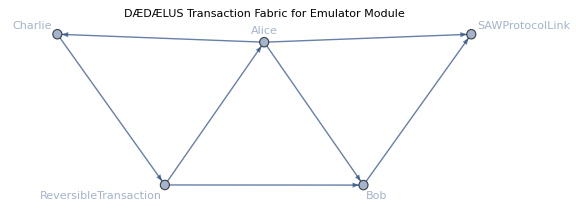

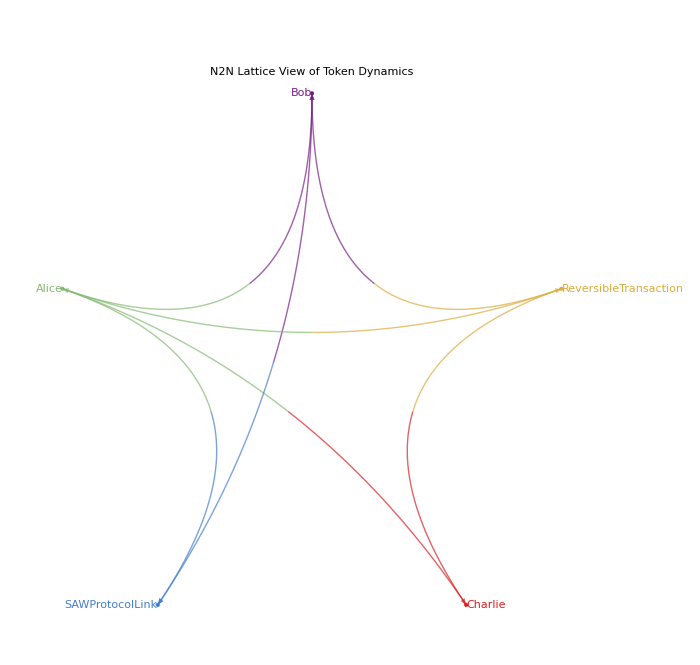

```mathematica
BeginPackage["Daedaelus`EthernetTopology`"];
CellAgentDependencies::usage="Finds other Cell Agents that are invoked or affected by the target Cell Agent, based on its DownValues and SubValues. This reveals the flow of conserved quantities and transactional state.";
GenerateTransactionFabricGraph::usage="GenerateTransactionFabricGraph[modules:{_String..}, opts___] generates a Transaction Fabric graph, visualizing the causal dependencies and message pathways between Cell Agents within specified system modules.";
FabricGraphAddAgentInfo::usage="FabricGraphAddAgentInfo[gr_Graph, opts___] enriches the Transaction Fabric graph with tooltips describing the role and philosophy of each Cell Agent.";
FabricGraphAddStatePrintButtons::usage="FabricGraphAddStatePrintButtons[gr_Graph, opts___] adds interactive buttons to the graph nodes, allowing for the inspection of a Cell Agent's live state or token definitions.";
VisualizeN2NLattice::usage="VisualizeN2NLattice[gr_Graph, opts___] applies a circular embedding to the fabric graph, ideal for visualizing the resilient topology of an N2N Lattice or Hypercell. Edges are rendered as Bezier curves to show the flow of causality.";
TraceTokenSourcePath::usage="TraceTokenSourcePath[gr_Graph, agent_?AtomQ, k_Integer:3] finds the causal history of a token or message arriving at a Cell Agent, tracing its path back up to k hops.";
TraceTokenDestinationPath::usage="TraceTokenDestinationPath[gr_Graph, agent_?AtomQ, k_Integer:3] shows the potential future pathways a token or message can take from a given Cell Agent, up to k hops forward.";
VisualizeLocalCausality::usage="VisualizeLocalCausality[gr_Graph, agent_?AtomQ, k_Integer:3] generates a subgraph showing the local interaction sphere of a Cell Agent, representing its Local Observer View (LOV) within the fabric.";
Begin["`Private`"];
Clear[SymbolQ];
SymbolQ[x_]:=Head[x]===Symbol;
ClearAll[FunctionQ];
SetAttributes[FunctionQ,HoldAll];
FunctionQ[sym_Symbol]:=(DownValues[sym]=!={}||SubValues[sym]=!={})&&OwnValues[sym]==={};
ClearAll[CellAgentDependencies];
Options[CellAgentDependencies]={"AtomicSymbols"->True};
SetAttributes[CellAgentDependencies,HoldFirst];
CellAgentDependencies[sym_Symbol,opts:OptionsPattern[]]:=Block[{atomicSymbolsQ},atomicSymbolsQ=TrueQ[OptionValue[CellAgentDependencies,"AtomicSymbols"]];With[{functionQ=If[atomicSymbolsQ,SymbolQ,FunctionQ]},Union[Join[List@@Select[Union[Level[(Hold@@DownValues[sym])⟦All,2⟧,{-1},Hold,Heads->True]],functionQ],List@@Select[Union[Level[(Hold@@SubValues[sym])⟦All,2⟧,{-1},Hold,Heads->True]],functionQ]]]]];
Clear[GenerateTransactionFabricGraph];
SyntaxInformation[GenerateTransactionFabricGraph]={"ArgumentsPattern"->{_,OptionsPattern[]}};
Options[GenerateTransactionFabricGraph]=Join[{"PrivateContexts"->False,"SelfReferencing"->False,"AtomicSymbols"->True,Exclusions->{},"UsageTooltips"->True,"UsageTooltipsStyle"->"Subsubsection"},Options[Graph]];
GenerateTransactionFabricGraph[context_String,opts:OptionsPattern[]]:=GenerateTransactionFabricGraph[{context},opts];
GenerateTransactionFabricGraph[contexts:{_String..},opts:OptionsPattern[]]:=Block[{pSymbs,pPrivateSymbs,exclSymbs,atomicSymbolsQ,dRes,aDependencyRules,gRules,grOpts,utStyle,styleFunc},pSymbs=Flatten[Function[{c},Block[{p=Names[c<>"*"]},Select[(ToExpression[c<>#1]&)/@p,SymbolQ]]]/@contexts];If[TrueQ[OptionValue[GenerateTransactionFabricGraph,"PrivateContexts"]],pPrivateSymbs=Flatten[(ToExpression[Names[#1<>"Private`*"]]&)/@contexts];pSymbs=Join[pSymbs,pPrivateSymbs];];atomicSymbolsQ=TrueQ[OptionValue[GenerateTransactionFabricGraph,"AtomicSymbols"]];pSymbs=If[atomicSymbolsQ,Select[pSymbs,SymbolQ],Select[pSymbs,FunctionQ]];exclSymbs=Flatten[{OptionValue[GenerateTransactionFabricGraph,Exclusions]}];pSymbs=Complement[pSymbs,exclSymbs];dRes=Association[(#1->CellAgentDependencies[#1,"AtomicSymbols"->atomicSymbolsQ]&)/@pSymbs];aDependencyRules=(pSymbs∩#1&)/@dRes;gRules=Flatten[Thread/@Normal[aDependencyRules]];If[!TrueQ[OptionValue[GenerateTransactionFabricGraph,"SelfReferencing"]],gRules=DeleteCases[gRules,x_->x_];];If[TrueQ[OptionValue[GenerateTransactionFabricGraph,"UsageTooltips"]],utStyle=OptionValue[GenerateTransactionFabricGraph,"UsageTooltipsStyle"];styleFunc=If[TrueQ[utStyle===None],Identity,Style[#1,utStyle]&];gRules=Map[Tooltip[#1,styleFunc[Row[{Style[SymbolName[#1],Italic,Bold],": ",ToString[MessageName[#1,"usage"]]}]]]&,gRules,{2}]];grOpts=Normal[KeyTake[{opts},First/@Options[Graph]]];If[TrueQ[OptionValue[GenerateTransactionFabricGraph,"UsageTooltips"]],Graph[gRules,Sequence@@grOpts,VertexLabels->"Name"],Graph[gRules,Sequence@@grOpts]]];
GenerateTransactionFabricGraph[___]:=Block[{},Message[GenerateTransactionFabricGraph::args];$Failed];
GenerateTransactionFabricGraph::args="The first argument is expected to be a string or a list of strings, each representing a system module or agent context.";
Clear[FabricGraphAddAgentInfo];
SyntaxInformation[FabricGraphAddAgentInfo]={"ArgumentsPattern"->{_,OptionsPattern[]}};
Options[FabricGraphAddAgentInfo]=Join[{"UsageTooltipsStyle"->"Subsubsection"},Options[Graph]];
FabricGraphAddAgentInfo[gr_Graph,opts:OptionsPattern[]]:=Block[{grOpts,utStyle,styleFunc,gRules},grOpts=FilterRules[{opts},Options[Graph]];utStyle=OptionValue[FabricGraphAddAgentInfo,"UsageTooltipsStyle"];styleFunc=If[TrueQ[utStyle===None],Identity,Style[#1,utStyle]&];gRules=Map[Tooltip[#1,styleFunc[Row[{Style[SymbolName[#1],Italic,Bold],": ",ToString[MessageName[#1,"usage"]]}]]]&,EdgeList[gr],{2}];Graph[gRules,Sequence@@grOpts,VertexLabels->"Name"]];
FabricGraphAddAgentInfo::args="The first argument must be a valid Transaction Fabric graph object.";
Clear[FabricGraphAddStatePrintButtons];
SyntaxInformation[FabricGraphAddStatePrintButtons]={"ArgumentsPattern"->{_,OptionsPattern[]}};
Options[FabricGraphAddStatePrintButtons]=Options[Graph];
FabricGraphAddStatePrintButtons[gr_Graph,opts:OptionsPattern[]]:=Block[{grDefRules},grDefRules=Map[Button[#1,GeneralUtilities`PrintDefinitions[#1],Appearance->Frameless]&,EdgeList[gr],{2}];Graph[grDefRules,opts,VertexLabels->"Name"]];
FabricGraphAddStatePrintButtons::args="The first argument must be a valid Transaction Fabric graph object.";
ClearAll[eSf,vSf];
eSf[g_,cols_,edgeThickness_:Thin,firstHalfEdgeFunc_:Line,secodHalfEdgeFunc_:Arrow]:=Module[{bsf=BSplineFunction[{#1⟦1⟧,RegionNearest[Disk[Mean[#1⟦{1,-1}⟧],Norm[#1⟦1⟧-#1⟦-1⟧]],{0,0}],#1⟦-1⟧}],p1=Subdivide[0,1/2,50],p2=Subdivide[1/2,1,50]},{edgeThickness,cols⟦VertexIndex[g,#2⟦1⟧]⟧,firstHalfEdgeFunc[bsf/@p1],cols⟦VertexIndex[g,#2⟦2⟧]⟧,secodHalfEdgeFunc[bsf/@p2]}]&;
vSf[g_,cols_,pointSize_:Large]:=Module[{off=If[-π/2<ArcTan@@#1<π/2,Left,Right]},{cols⟦VertexIndex[g,#2]⟧,Text[Style[Framed[#2,FrameStyle->None],FontSize->Scaled[.03]],#1,{off,Center},ArcTan[#1] (off/.{Left->1,Right->-1})],PointSize[pointSize],Point[#1]}]&;
Clear[VisualizeN2NLattice];
SyntaxInformation[VisualizeN2NLattice]={"ArgumentsPattern"->{_,OptionsPattern[]}};
Options[VisualizeN2NLattice]=Join[{"VertexColors"->Automatic,"EdgeThickness"->Automatic},Options[Graph]];
VisualizeN2NLattice[gr_Graph,opts:OptionsPattern[]]:=Block[{cc,cols,grOpts,edgeThickness},cols=OptionValue["VertexColors"];If[TrueQ[cols===Automatic],cc=PageRankCentrality[gr];cols=ColorData[{"Rainbow",{1,VertexCount[gr]}}]/@Range[VertexCount[gr]];cols=cols⟦Ordering[cc]⟧;];grOpts=Normal[KeyTake[{opts},First/@Options[Graph]]];edgeThickness=OptionValue["EdgeThickness"];If[TrueQ[edgeThickness===Automatic],edgeThickness=If[EdgeCount[gr]/(VertexCount[gr]+1)>1.5||EdgeCount[gr]>400,Thin,Thick,Thin]];Graph[EdgeList[gr],Sequence@@grOpts,VertexLabels->None,GraphLayout->"CircularEmbedding",VertexShapeFunction->vSf[gr,cols],EdgeShapeFunction->eSf[gr,cols,edgeThickness]]];
VisualizeN2NLattice::args="The first argument must be a valid Transaction Fabric graph object.";
Clear[TraceTokenSourcePath];
SyntaxInformation[TraceTokenSourcePath]={"ArgumentsPattern"->{_,_,_.}};
TraceTokenSourcePath[gr_Graph,node_?AtomQ,n_Integer:3]:=Union[Flatten[Rest[NestList[Flatten[(Cases[EdgeList[gr],_->#1]&)/@#1⟦All,1⟧]&,{node->node},n]]]]/;n≥0;
TraceTokenSourcePath::args="Arguments are: a graph object, a graph vertex (Cell Agent), and an optional non-negative integer for path length.";
Clear[TraceTokenDestinationPath];
SyntaxInformation[TraceTokenDestinationPath]={"ArgumentsPattern"->{_,_,_.}};
TraceTokenDestinationPath[gr_Graph,node_Symbol,n_Integer:3]:=Union[Flatten[Rest[NestList[Flatten[(Cases[EdgeList[gr],#1->_]&)/@#1⟦All,2⟧]&,{node->node},n]]]]/;n≥0;
TraceTokenDestinationPath::args="Arguments are: a graph object, a graph vertex (Cell Agent), and an optional non-negative integer for path length.";
Clear[VisualizeLocalCausality];
SyntaxInformation[VisualizeLocalCausality]={"ArgumentsPattern"->{_,_,_.}};
VisualizeLocalCausality[gr_Graph,node_Symbol,n_Integer:3]:=Union[Flatten[Rest[NestList[Flatten[(Cases[EdgeList[gr],#1->_|_->#1]&)/@Union[Flatten[List@@@#1]]]&,{node->node},n]]]]/;n≥0;
VisualizeLocalCausality::args="Arguments are: a graph object, a graph vertex (Cell Agent), and an optional non-negative integer for path length.";
End[];
EndPackage[]
BeginPackage["Daedaelus`Emulator`"];
Alice::usage="Alice: Initiates a reversible transaction by emitting a French Token.";
Bob::usage="Bob: Responds to Alice and manages the corresponding German Token.";
Charlie::usage="Charlie (Captain, Coordinator): Observes the Alice-Bob interaction and ensures token conservation across the link, enabling the TIKTYKTIK property ('I Know That You Know That I Know').";
SAWProtocolLink::usage="SAWProtocolLink: Manages the stateful, bidirectional communication object between two cells, ensuring atomicity.";
ReversibleTransaction::usage="ReversibleTransaction: A higher-level construct that uses Reversible Subtransactions to guarantee atomicity without resorting to the 'irreversible smash and restart of Shannon information.'";
Begin["`Private`"];
Alice[]:=(SAWProtocolLink["French Token"];Bob["French Token"];Charlie["Observe","Alice","Bob"];);
Bob[token_]:=(SAWProtocolLink["German Token"];);
Charlie[action_,from_,to_]:=(ReversibleTransaction[{from,to}];);
ReversibleTransaction[agents_List]:=(Alice;Bob;);
End[];
EndPackage[];
fabricGraph=GenerateTransactionFabricGraph["Daedaelus`Emulator`",GraphLayout->"SpringElectricalEmbedding",ImageSize->Large,PlotLabel->Style["DÆDÆLUS Transaction Fabric for Emulator Module",Bold,16]]
VisualizeN2NLattice[fabricGraph,ImageSize->700,PlotLabel->Style["N2N Lattice View of Token Dynamics",Bold,16]]
```

Resilience to Random Failures

Lastly, the code simulates random edge failures to directly test network survivability. It incrementally removes a certain number of random links from each network and checks how many connected components remain. In a perfectly resilient network, even with several link failures, most nodes would still be in one giant component (i.e. the network stays mostly connected). In a fragile network, removing just a couple of key links could break it into multiple isolated groups. The simulation results show a clear difference: the Clos network quickly fragments as edges are removed, whereas the mesh network remains largely connected until many more failures occur. For instance, removing 1–2 links in the Clos might disconnect some servers entirely (e.g. cut the only path from a rack to the rest), raising the number of components. In contrast, the mesh typically still has alternate routes after a few random cuts, so all nodes remain in one component. Only after several links are removed does the mesh start to split into multiple components. This aligns with Baran’s survivability criterion: in a distributed network, a high fraction of nodes will remain connected as one group even under heavy attack, whereas in a hierarchical network a smaller amount of damage can isolate nodes into small, ineffective islands (https://www.rand.org/pubs/research_memoranda/RM3420.html#:~:text=enemy%20attack,are%20considered%20to%20be%20ineffective & https://www.rand.org/pubs/research_memoranda/RM3420.html#:~:text=enemy%20attack,of%20the%20surviving%20stations%20to). The redundancy level of the lattice is much higher, meaning many links would have to fail before communication is truly disrupted (https://www.rand.org/pubs/research_memoranda/RM3420.html#:~:text=,paramount%20interest). By contrast, the Clos has critical cut points. (Think of a hub-and-spoke: cut one spoke and that node is lost; the Clos is not that extreme, but still has chokepoints like the single uplink from each server and limited uplinks from each rack.)

This resilience experiment underscores a key trade-off in network design. Clos/fat-tree topologies are engineered for capacity and scalability, and they do have some fault tolerance (multiple spines, etc.), but they are optimized for expected patterns of failure and may not handle worst-case random failures as gracefully. Distributed meshes like the N2N lattice take the opposite approach: assume links can fail anywhere and ensure the network can heal and route around almost any such failure. The result is an extremely survivable network – one that, as Baran put it, requires an adversary (or a disaster) to destroy nearly all nodes or links to completely break it (https://www.rand.org/pubs/research_memoranda/RM3420.html#:~:text=We%20will%20soon%20be%20living,shown%20that%20highly%20survivable%20system & https://www.rand.org/pubs/research_memoranda/RM3420.html#:~:text=destruction%20requires%20the%20enemy%20to,shown%20that%20highly%20survivable%20system). Such a network can degrade gracefully: performance may drop as links fail, but connectivity remains, which is crucial for mission-critical systems.

```mathematica
ClearAll["Global`*"];
cellStyle={FontFamily->"Palatino",FontSize->14};
plotStyle={FontFamily->"Helvetica",FontSize->12};
titleStyle={FontFamily->"Helvetica",FontSize->24,FontWeight->"Bold",TextAlignment->Center};
subtitleStyle={FontFamily->"Helvetica",FontSize->18,FontWeight->"Bold",TextAlignment->Center};
headerStyle={FontFamily->"Helvetica",FontSize->16,FontWeight->"Bold"};
commentStyle={FontFamily->"Palatino",FontSize->12,FontColor->Gray};
infoPanel[title_String,content_List]:=Framed[Grid[Prepend[content,{Style[title,Bold,14],}],Alignment->{Left,Center},Spacings->{2,1.5}],RoundingRadius->5,Background->RGBColor[0.97,0.97,0.97],FrameStyle->LightGray];
Print[Style["Part 1: The Classical 1976 Ethernet Model",subtitleStyle]];
Print[Style["We begin by recreating the seminal model developed by Metcalfe and Boggs. This model describes a shared, passive Ether where control is distributed among contending stations. Coordination is achieved through statistical arbitration. When the Ether is busy, stations defer; when multiple stations transmit simultaneously, they collide, abort, and randomly reschedule. This model was foundational, but as we will demonstrate, its reliance on statistical contention leads to a collapse in efficiency under load.",Sequence@@cellStyle]];
acquisitionProbability[q_]:=If[q≤1,1,(1-1/q)^(q-1)];
meanWaitSlots[a_]:=If[a==0,∞,(1-a)/a];
ethernetEfficiency[packetSizeBits_,channelCapacityBps_,slotTimeSec_,qStations_]:=Module[{a=acquisitionProbability[qStations],pOC=packetSizeBits/channelCapacityBps,w},w=meanWaitSlots[a];If[w===∞,0,pOC/(pOC+w slotTimeSec)]];
Manipulate[Module[{efficiency=ethernetEfficiency[p,cap,t,q],a=acquisitionProbability[q],w=meanWaitSlots[a]},Column[{Show[Plot[ethernetEfficiency[p,cap,t,x],{x,1,256},PlotRange->{{0,256},{0,1}},Frame->True,FrameLabel->{Style["Q (Number of Contending Stations)",Bold],Style["Efficiency (E)",Bold]},PlotLabel->Style["Classical Ethernet Efficiency vs. Contention",Bold],Epilog->{Red,PointSize[Large],Point[{q,efficiency}]},GridLines->Automatic,ImageSize->Large,BaseStyle->plotStyle],ImagePadding->20],Spacer[15],infoPanel["Metcalfe Model Parameters",{{"Packet Size (P)",Row[{p," bits"}]},{"Ethernet Capacity (C)",Row[{NumberForm[cap/10^6,{4,2}]," Mbps"}]},{"Slot Time (T)",Row[{NumberForm[t 10^6,{4,2}]," μs (round-trip contention slot)"}]},{"Contending Stations (Q)",Style[q,Bold]},{"Acquisition Probability (A)",Style[NumberForm[N[a],{3,3}],Bold,Red]},{"Mean Wait Slots (W)",Style[If[w===∞,"∞",NumberForm[N[w],{3,3}]],Bold,Red]},{"Calculated Efficiency (E)",Style[ToString[Round[efficiency 100,0.1]]<>"%",Bold,Red]}}]}]],{{p,4096,"Packet Size (P) [bits]"},{512,1024,4096}},{{cap,3 10^6,"Channel Capacity (C) [bps]"},1 10^6,10 10^6,Appearance->"Labeled"},{{t,16/10^6,"Slot Time (T) [sec]"},1/10^6,50/10^6,Appearance->"Labeled"},{{q,32,"Contending Stations (Q)"},1,256,1,Appearance->"Labeled"},ControlPlacement->Left];
Print[Style["Part 2: The DÆDÆLUS Protocol Model",subtitleStyle]];
Print[Style["Now we model the DÆDÆLUS protocol on a point-to-point link. This architecture escapes the contention-based model entirely. The critical insight relates the packet's transmission time to the signal's propagation time. When a packet is 'longer than the wire' — that is, its transmission time exceeds the round-trip propagation delay — the link becomes fully utilized. The sender receives the acknowledgment for the head of the packet before the tail of the packet has even left its transceiver. This geometric relationship makes reliability effectively free under the right regime.",Sequence@@cellStyle]];
daedalusEfficiency[txTime_,propTime_]:=Min[1,txTime/(2 propTime)];
Manipulate[Module[{cLight=299792458 0.66,txTime=packetSize/bandwidth,propTime=linkLength/cLight,efficiency},efficiency=daedalusEfficiency[txTime,propTime];Column[{Plot[daedalusEfficiency[packetSize/bandwidth,x/cLight],{x,1,2000},PlotRange->{{0,2000},{0,1.1}},Frame->True,FrameLabel->{Style["Link Length (meters)",Bold],Style["Efficiency",Bold]},PlotLabel->Style["DÆDÆLUS Protocol Efficiency vs. Link Length",Bold],Epilog->{Red,PointSize[Large],Point[{linkLength,efficiency}]},GridLines->Automatic,ImageSize->Large,BaseStyle->plotStyle],Spacer[15],infoPanel["DÆDÆLUS Protocol Parameters",{{"Packet Size (bits)",Row[{packetSize," bits"}]},{"Bandwidth",Row[{NumberForm[bandwidth/10^9,{3,2}]," Gbps"}]},{"Link Length",Style[Row[{linkLength," meters"}],Bold]},{"Transmission Time (t_tx)",Style[Row[{NumberForm[txTime 10^9,{4,2}]," ns"}],Bold,Red]},{"Round-Trip Propagation Time (2 t_prop)",Style[Row[{NumberForm[2 propTime 10^9,{4,2}]," ns"}],Bold,Red]},{"Is packet longer than the wire?",Style[If[txTime>2 propTime,"Yes","No"],Bold,Red]},{"Calculated Efficiency",Style[ToString[Round[efficiency 100,0.1]]<>"%",Bold,Red]}}]}]],{{packetSize,12000,"Packet Size (bits)"},1000,24000,100,Appearance->"Labeled"},{{bandwidth,10000000000,"Bandwidth"},{{1000000000,"1 Gbps"},{10000000000,"10 Gbps"},{40000000000,"40 Gbps"},{100000000000,"100 Gbps"}},ControlType->PopupMenu},{{linkLength,3,"Link Length (m)"},1,2000,1,Appearance->"Labeled"},ControlPlacement->Left];
Print[Style["Part 3: The Efficiency Showdown",subtitleStyle]];
Print[Style["Here we provide the definitive visual proof. We plot the efficiency of both models on the same axes. The classical Ethernet model, fundamentally limited by statistical contention, collapses under high competitor counts. In contrast, the DÆDÆLUS protocol on a point-to-point link maintains near-perfect efficiency when the packet is longer than the wire. This contrast foregrounds the core Daedaelus critique: probabilistic contention divides epistemic state and sacrifices efficiency, whereas geometry (longer-than-wire) yields certainty.",Sequence@@cellStyle]];
Manipulate[Module[{cLight=299792458 0.66,slotTime,ethEff,daedalusEff},slotTime=(2 linkLength)/cLight;ethEff=ethernetEfficiency[p,cap,slotTime,q];daedalusEff=daedalusEfficiency[p/cap,linkLength/cLight];Column[{Plot[{ethEff/.q->x,daedalusEff},{x,1,256},PlotRange->{{0,256},{0,1.1}},Frame->True,FrameLabel->{Style["Q (Number of Contending Stations)",Bold],Style["Efficiency",Bold]},PlotLabel->Style["Efficiency Showdown: DÆDÆLUS vs. Classical Ethernet",Bold],PlotLegends->Placed[LineLegend[{Style["Classical Ethernet",Thick],Style["DÆDÆLUS Protocol",Thick,Dashed]},{"Classical Ethernet","DÆDÆLUS Protocol"},LegendLabel->Style["Model",Bold]],{Right,Center}],GridLines->Automatic,ImageSize->Large,BaseStyle->plotStyle,Epilog->{{Red,PointSize[Large],Point[{q,ethEff}],Text[Style["Classic E",Bold,12],{q,ethEff},{1,-1}]},{Blue,PointSize[Large],Point[{q,daedalusEff}],Text[Style["DÆDÆLUS",Bold,12],{q,daedalusEff},{1,1}]}},PlotStyle->{{Thick,ColorData[97][1]},{Thick,Dashed,ColorData[97][2]}}],Spacer[15],infoPanel["Showdown Parameters",{{"Packet Size (P)",Row[{p," bits"}]},{"Effective Capacity (C)",Row[{NumberForm[cap/10^9,{3,2}]," Gbps"}]},{"Link Length (meters)",Style[linkLength,Bold]},{"Classical Ethernet Efficiency at Q",Style[ToString[Round[ethEff 100,0.1]]<>"%",Red,Bold]},{"DÆDÆLUS Protocol Efficiency",Style[ToString[Round[daedalusEff 100,0.1]]<>"%",Blue,Bold]}}]}]],{{p,12000,"Packet Size (P) [bits]"},4096,24000,1024,Appearance->"Labeled"},{{cap,10000000000,"Capacity (C) [bps]"},{{1000000000,"1 Gbps"},{10000000000,"10 Gbps"},{40000000000,"40 Gbps"}},ControlType->PopupMenu},{{linkLength,10,"Link Length (meters)"},1,100,1,Appearance->"Labeled"},{{q,32,"Contending Stations (Q)"},1,256,1,Appearance->"Labeled"},ControlPlacement->Top];
Print[Style["Conclusion",subtitleStyle]];
Print[Style["The classical model is bound by the dynamics of collision and backoff, forcing a trade-off between utilization and fairness that breaks down under load. The DÆDÆLUS model is constrained only by physics — the speed of signal propagation and transmission duration. By moving from a shared, contended Ether to a lattice of reliable point-to-point links and invoking the 'longer than the wire' principle, we demonstrate that high efficiency and strong reliability need not be antagonistic. This provides a rigorous, geometric foundation for the Daedaelus argument and the design of Open Atomic Ethernet.",Sequence@@cellStyle]];
```

Part 1: The Classical 1976 Ethernet Model

We begin by recreating the seminal model developed by Metcalfe and Boggs. This model describes a shared, passive Ether where control is distributed among contending stations. Coordination is achieved through statistical arbitration. When the Ether is busy, stations defer; when multiple stations transmit simultaneously, they collide, abort, and randomly reschedule. This model was foundational, but as we will demonstrate, its reliance on statistical contention leads to a collapse in efficiency under load.

Part 2: The DÆDÆLUS Protocol Model

Now we model the DÆDÆLUS protocol on a point-to-point link. This architecture escapes the contention-based model entirely. The critical insight relates the packet's transmission time to the signal's propagation time. When a packet is 'longer than the wire' — that is, its transmission time exceeds the round-trip propagation delay — the link becomes fully utilized. The sender receives the acknowledgment for the head of the packet before the tail of the packet has even left its transceiver. This geometric relationship makes reliability effectively free under the right regime.

Part 3: The Efficiency Showdown

Here we provide the definitive visual proof. We plot the efficiency of both models on the same axes. The classical Ethernet model, fundamentally limited by statistical contention, collapses under high competitor counts. In contrast, the DÆDÆLUS protocol on a point-to-point link maintains near-perfect efficiency when the packet is longer than the wire. This contrast foregrounds the core Daedaelus critique: probabilistic contention divides epistemic state and sacrifices efficiency, whereas geometry (longer-than-wire) yields certainty.

Conclusion

The classical model is bound by the dynamics of collision and backoff, forcing a trade-off between utilization and fairness that breaks down under load. The DÆDÆLUS model is constrained only by physics — the speed of signal propagation and transmission duration. By moving from a shared, contended Ether to a lattice of reliable point-to-point links and invoking the 'longer than the wire' principle, we demonstrate that high efficiency and strong reliability need not be antagonistic. This provides a rigorous, geometric foundation for the Daedaelus argument and the design of Open Atomic Ethernet.

## Conclusion

The comparison between the N2N lattice and traditional topologies highlights the benefits of fully distributed networking. The N2N lattice (modeled here with a hexagonal neighbor-to-neighbor mesh) provides multiple independent paths and enables fast self-healing via spanning tree reconfiguration. This yields a network that is highly resilient: it can tolerate numerous failures while still keeping most nodes connected, reflecting the principles first identified by Paul Baran in the 1960s for survivable communications (https://www.rand.org/pubs/research_memoranda/RM3420.html#:~:text=Figure%201,Distributed%20Networks & https://www.rand.org/pubs/research_memoranda/RM3420.html#:~:text=II,Network). The lattice also offers the potential for consistent low-latency communication, since traffic doesn’t have to traverse vertical layers of hierarchy and can instead take short hops between neighbors – a design goal of the DÆDÆLUS architecture for achieving deterministic performance (https://mulliganstew-gang.vercel.app/#:~:text=with%20the%20D%C3%A6d%C3%A6lus%20architecture%2C%20simulating,%C2%BB). 

By contrast, the Clos (fat-tree) topology, representative of modern data center networks, shows good performance under normal conditions and some built-in redundancy (https://synchronet.net/what-is-clos-architecture/#:~:text=How%20do%20Clos%20Networks%20Support,Scalability%20and%20Fault%20Tolerance), but its hierarchical nature makes it inherently less flexible against failures. A Clos network has significantly fewer alternate spanning trees and can be partitioned by targeted link or switch failures (for example, losing a top-of-rack switch or a critical spine link can cut off many devices). While Clos networks do support multiple paths and are considered fault-tolerant in practice, their resilience is limited compared to a richly-meshed lattice. The experiments above quantified this: the distributed mesh had orders of magnitude more spanning trees and withstood random link removals with minimal loss of connectivity, whereas the Clos began to fragment with just a few failures.

```mathematica
ClearAll["Global`*"];
cellStyle={FontFamily->"Palatino",FontSize->14};
plotStyle={FontFamily->"Helvetica",FontSize->12};
titleStyle={FontFamily->"Helvetica",FontSize->24,FontWeight->"Bold",TextAlignment->Center};
subtitleStyle={FontFamily->"Helvetica",FontSize->18,FontWeight->"Bold",TextAlignment->Center};
headerStyle={FontFamily->"Helvetica",FontSize->16,FontWeight->"Bold"};
commentStyle={FontFamily->"Palatino",FontSize->12,FontColor->Gray};
infoPanel[title_String,content_List]:=Framed[Grid[Prepend[content,{Style[title,Bold,14],}],Alignment->{Left,Center},Spacings->{2,1.5}],RoundingRadius->5,Background->RGBColor[.97,.97,.97],FrameStyle->LightGray,FrameMargins->8];
acquisitionProbability[q_?Positive]:=If[q≤1,1.,(1-1./q)^(q-1)];
meanWaitSlots[a_]:=If[a==0,∞,(1-a)/a];
ethernetEfficiency[packetSizeBits_,channelCapacityBps_,slotTimeSec_,qStations_]:=Module[{a,pOC,w},a=acquisitionProbability[qStations];pOC=packetSizeBits/channelCapacityBps;w=meanWaitSlots[a];If[w===∞,0,pOC/(pOC+w slotTimeSec)]];
daedalusEfficiency[txTime_,propTime_]:=Min[1,txTime/(2 propTime)];
DynamicModule[{packetSizeClassic=4096,capacityClassic=3 10^6,slotTime=16./10^6,qStations=32,packetSizeDaedalus=12000,bandwidthDaedalus=10^10,linkLength=3},Column[{Style["Part 1: The Classical 1976 Ethernet Model",subtitleStyle],Style["Recreation of the Metcalfe & Boggs shared Ether with statistical contention and back-off.  Efficiency collapses under load as the number of competing stations grows.",Sequence@@cellStyle],Spacer[10],Row[{Panel[Dynamic[Module[{effClassic=ethernetEfficiency[packetSizeClassic,capacityClassic,slotTime,qStations],a=acquisitionProbability[qStations],w=meanWaitSlots[acquisitionProbability[qStations]]},Column[{Show[Plot[ethernetEfficiency[packetSizeClassic,capacityClassic,slotTime,x],{x,1,256},PlotRange->{{0,256},{0,1}},Frame->True,FrameLabel->{Style["Q (Number of Contending Stations)",Bold],Style["Efficiency (E)",Bold]},PlotLabel->Style["Classical Ethernet Efficiency vs. Contention",Bold],Epilog->{Red,PointSize[Large],Point[{qStations,effClassic}]},GridLines->Automatic,ImageSize->450,BaseStyle->plotStyle,PlotStyle->Thick],ImageSize->450],Spacer[6],infoPanel["Metcalfe Model Parameters",{{"Packet Size (P)",Row[{packetSizeClassic," bits"}]},{"Ether Capacity (C)",Row[{NumberForm[N[capacityClassic/10.^6],{3,2}]," Mbps"}]},{"Slot Time (T)",Row[{NumberForm[N[slotTime 10.^6],{3,2}]," μs (contention unit)"}]},{"Contending Stations (Q)",Style[qStations,Bold]},{"Acquisition Probability (A)",Style[NumberForm[N[a],{3,4}],Bold,Red]},{"Mean Wait Slots (W)",Style[If[w===∞,"∞",NumberForm[N[w],{3,3}]],Bold,Red]},{"Calculated Efficiency (E)",Style[ToString[Round[effClassic 100,0.1]]<>"%",Bold,Red]}}]}]]],"Classical Ethernet"],Spacer[20],Panel[Column[{Style["Classical Ethernet Controls",headerStyle],Spacer[4],Row[{"Packet Size (bits): ",Slider[Dynamic[packetSizeClassic],{512,16384,512},ImageSize->Medium],Dynamic[packetSizeClassic]}],Row[{"Channel Capacity (Mbps): ",Slider[Dynamic[capacityClassic],{1 10^6,10 10^6,5 10^5},ImageSize->Medium],Dynamic[NumberForm[N[capacityClassic/10.^6],{3,2}]]}],Row[{"Slot Time (μs): ",Slider[Dynamic[slotTime],{1./10^6,50./10^6,1./10^6},ImageSize->Medium],Dynamic[NumberForm[N[slotTime 10.^6],{3,2}]]}],Row[{"Q Stations: ",Slider[Dynamic[qStations],{1,256,1},ImageSize->Medium],Dynamic[qStations]}]}],"Parameters"]}],Style["Part 2: The DÆDÆLUS Protocol Model",subtitleStyle],Style["Point-to-point link: escaping contention via the “longer-than-the-wire” geometric principle.  Reliability approaches 100 % when transmission time exceeds round-trip propagation.",Sequence@@cellStyle],Spacer[10],Row[{Panel[Dynamic[Module[{cLight=299792458 0.66,txTime=packetSizeDaedalus/bandwidthDaedalus,propTime=linkLength/(299792458 0.66),effDae},effDae=daedalusEfficiency[txTime,propTime];Column[{Show[Plot[daedalusEfficiency[packetSizeDaedalus/bandwidthDaedalus,x/(299792458 0.66)],{x,1,2000},PlotRange->{{0,2000},{0,1.1}},Frame->True,FrameLabel->{Style["Link Length (meters)",Bold],Style["Efficiency",Bold]},PlotLabel->Style["DÆDÆLUS Protocol Efficiency vs. Link Length",Bold],Epilog->{Red,PointSize[Large],Point[{linkLength,effDae}]},GridLines->Automatic,ImageSize->450,BaseStyle->plotStyle,PlotStyle->Thick],ImageSize->450],Spacer[6],infoPanel["DÆDÆLUS Protocol Parameters",{{"Packet Size (bits)",Row[{packetSizeDaedalus," bits"}]},{"Bandwidth",Row[{NumberForm[N[bandwidthDaedalus/10.^9],{3,2}]," Gbps"}]},{"Link Length",Style[Row[{linkLength," meters"}],Bold]},{"Transmission Time (t_tx)",Style[Row[{NumberForm[N[txTime 10.^9],{3,2}]," ns"}],Bold,Red]},{"Round-Trip Propagation Time (2 t_prop)",Style[Row[{NumberForm[N[2 propTime 10.^9],{3,2}]," ns"}],Bold,Red]},{"Is packet “longer than the wire”?",Style[If[txTime>2 propTime,"Yes","No"],Bold,Red]},{"Calculated Efficiency",Style[ToString[Round[effDae 100,0.1]]<>"%",Bold,Red]}}]}]]],"DÆDÆLUS Protocol"],Spacer[20],Panel[Column[{Style["DÆDÆLUS Protocol Controls",headerStyle],Spacer[4],Row[{"Packet Size (bits): ",Slider[Dynamic[packetSizeDaedalus],{1000,24000,100},ImageSize->Medium],Dynamic[packetSizeDaedalus]}],Row[{"Bandwidth (Gbps): ",PopupMenu[Dynamic[bandwidthDaedalus],{1 10^9->"1 Gbps",10 10^9->"10 Gbps",40 10^9->"40 Gbps",100 10^9->"100 Gbps"}],Dynamic[NumberForm[N[bandwidthDaedalus/10.^9],{3,0}]]}],Row[{"Link Length (m): ",Slider[Dynamic[linkLength],{1,2000,1},ImageSize->Medium],Dynamic[linkLength]}]}],"Parameters"]}],Style["Part 3: The Efficiency Showdown",subtitleStyle],Style["Overlay of Classical Ethernet vs. DÆDÆLUS protocol efficiency to make the fundamental contrast explicit.",Sequence@@cellStyle],Spacer[10],Panel[Dynamic[Module[{cLight=299792458 0.66,txTimeClassic=packetSizeClassic/capacityClassic,slotRoundTrip=(2 linkLength)/(299792458 0.66),effClassicShowdown,effDaeShowdown},effClassicShowdown=ethernetEfficiency[packetSizeClassic,capacityClassic,slotRoundTrip,qStations];effDaeShowdown=daedalusEfficiency[packetSizeClassic/capacityClassic,linkLength/(299792458 0.66)];Column[{Show[Plot[{ethernetEfficiency[packetSizeClassic,capacityClassic,slotRoundTrip,x],daedalusEfficiency[packetSizeClassic/capacityClassic,linkLength/(299792458 0.66)]},{x,1,256},PlotRange->{{0,256},{0,1.1}},Frame->True,FrameLabel->{Style["Q (Number of Contending Stations)",Bold],Style["Efficiency",Bold]},PlotLabel->Style["Efficiency Showdown: DÆDÆLUS vs. Classic Ethernet",Bold],PlotLegends->Placed[LineLegend[{Style["Classic Ethernet",Thick],Style["DÆDÆLUS Protocol",Thick,Dashed]},LegendLabel->Style["Model",Bold]],{Right,Center}],GridLines->Automatic,ImageSize->650,BaseStyle->plotStyle,PlotStyle->{Thick,{Thick,Dashed}}],ImageSize->650],Spacer[6],Row[{infoPanel["Showdown Snapshot",{{"Classical Efficiency at Q="<>ToString[qStations],Style[ToString[Round[effClassicShowdown 100,0.1]]<>"%",Bold,Red]},{"DÆDÆLUS Efficiency (same parameters)",Style[ToString[Round[effDaeShowdown 100,0.1]]<>"%",Bold,Red]}}]}]}]]],"Efficiency Showdown"],Style["Conclusion",subtitleStyle],Style["The classical model is limited by stochastic collisions and back-off, forcing an inherent trade-off between fairness and utilization; efficiency collapses under load.  The DÆDÆLUS model, grounded in deterministic geometry (transmission time vs. propagation delay), achieves near-100 % utilization without contention.  This demonstrates that shared-bandwidth statistical multiplexing inevitably loses epistemic state through re-arbitration, whereas transaction-aware point-to-point links (the DÆDÆLUS lens) avoid those losses entirely.",Sequence@@cellStyle]}]]
```

In summary, a decentralized lattice topology can greatly enhance network robustness and reliability, aligning with the growing interest in distributed network architectures for modern needs (https://www.liveaction.com/resources/blog-post/centralized-vs-decentralized-vs-distributed-networks-the-history-future/#:~:text=decentralized%20network%20in%20a%20proposal,for%20the%20US%20AirForce & https://www.liveaction.com/resources/blog-post/centralized-vs-decentralized-vs-distributed-networks-the-history-future/#:~:text=Despite%20this%20early%20realization%20that,end%20of%20a%20Russian%20cyberattack). The DÆDÆLUS project’s approach of managing such a topology with a Graph Virtual Machine (using spanning trees and reversible protocols) is an example of leveraging this old-but-new idea: building networks that favor resilience and consistent performance over the simplicity of centralized control. As networks become ever more critical (and as downtime or data loss becomes less acceptable), these distributed designs are gaining renewed attention. This deep dive into the code’s simulation confirms that moving “beyond the tree” to an N2N lattice can indeed provide superior resilience by design (https://mulliganstew-gang.vercel.app/#:~:text=Alternating%20Bit%20Protocol%2C%20demonstrating%20the,%C2%BB), ensuring that no single failure can bring down the entire system.

```mathematica
acquisitionProbability[Q_]:=(1-1/Q)^(Q-1);
meanWaitingSlots[Q_]:=(1-acquisitionProbability[Q])/acquisitionProbability[Q];
classicalEthernetEfficiency[P_,C_,T_,Q_]:=Module[{W=meanWaitingSlots[Q],PoverC},PoverC=P/C;PoverC/(PoverC+W T)];
packetTransmissionTime[packetSizeInBytes_,linkSpeedBps_]:=(packetSizeInBytes 8)/linkSpeedBps;
roundTripPropagationDelay[linkLengthM_,propagationSpeedMps_]:=(2 linkLengthM)/propagationSpeedMps;
aethernetLinkUtilization[packetSizeInBytes_,linkSpeedBps_,linkLengthM_,propagationSpeedMps_]:=Module[{transmissionTime=packetTransmissionTime[packetSizeInBytes,linkSpeedBps],roundTripTime=roundTripPropagationDelay[linkLengthM,propagationSpeedMps]},transmissionTime/(transmissionTime+Max[0,roundTripTime-transmissionTime])];
Manipulate[Module[{bitsPerPacket=packetSizeInBytes 8,propSpeed=2.0 10^8},LogLogPlot[{classicalEthernetEfficiency[bitsPerPacket,linkSpeedBps,roundTripPropagationDelay[linkLengthM,propSpeed],contendingStationsQ],aethernetLinkUtilization[packetSizeInBytes,linkSpeedBps,linkLengthM,propSpeed]},{linkLengthM,0.01,1000},PlotRange->{{0.01,1000},{0,1.1}},AxesLabel->{"N2N Link Length (meters)","Link Utilization / Efficiency"},PlotLabel->Style["Efficiency Showdown:\nClassical Contention vs. Deterministic Interaction",18],PlotLegends->Placed[LineLegend[{"Classical Ethernet (Metcalfe Model)","Open Atomic Ethernet (D\\[ae]d\\[ae]lus Model)"},LegendLayout->"Column"],{0.25,0.3}],GridLines->Automatic,ImageSize->Large,Epilog->{Text[Style[StringTemplate["Packet is 'longer than the wire' when length < ``m"][NumberForm[packetTransmissionTime[packetSizeInBytes,linkSpeedBps] propSpeed,{3,2}]],Gray,12],{1,0.9},{-1.5,0}],{Gray,Dashed,Line[{{packetTransmissionTime[packetSizeInBytes,linkSpeedBps] propSpeed,0},{packetTransmissionTime[packetSizeInBytes,linkSpeedBps] propSpeed,1}}]}}]],{{linkSpeedBps,100 10^9,"Link Speed"},{10 10^9->"10 Gbps",25 10^9->"25 Gbps",100 10^9->"100 Gbps",400 10^9->"400 Gbps"}},{{packetSizeInBytes,64,"Packet Size"},{64->"64 Bytes (Min)",512->"512 Bytes",1518->"1518 Bytes (Max)"}},{{contendingStationsQ,32,"Contending Stations (Q)"},2,256,1,Appearance->"Labeled"},ControlPlacement->Left]
```

## ‘Code as Proof’ Efficiency Model

This Mathematica notebook serves as a form of “code as proof,” re-examining the foundational assumptions that have governed Ethernet for five decades. It provides a definitive, visual showdown between two paradigms. The first is the classical Metcalfe model for a shared, best-effort Ether, a system that embraces statistical contention and pushes reliability to higher layers, forcing applications to rely on timeouts and retries. This model quantifies a world where acknowledgements were considered expensive and bandwidth was throttled by the need for reliability.

The second paradigm is the Open Atomic Ethernet model for a reliable, point-to-point N2N link. This model proves that on modern high-speed, short-distance links, acknowledgements are not only inexpensive—they are virtually free. It demonstrates the “longer than the wire” concept, where a packet’s transmission time can exceed its round-trip propagation delay. In this regime, an acknowledgment is received before the sender has even finished transmitting, creating a “circulating snake” of bits that achieves nearly 100% link utilization. This proves that you cannot add reliability on top of an unreliable network; it must be built into the foundation. The analysis provides the definitive proof that the industry must shift its focus from multiplexing raw bandwidth to multiplexing the “transactional capacity of the link,” enabling exactly-once semantics without sacrificing performance.

--- Simulation Event Log ---

Time 0s: System Simulation Start. Link RTT:    517
---------
500000000s

Time 0s: Alice Sends. Packet1 (Alt: 0)

Time 5.0000000000*10^-9s: Bob Receives. Packet1 (Alt: 0)

Time 5.0000000000*10^-9s: Bob Accepts. Packet1 (Alt: 0)

Time 5.0000000000*10^-9s: Bob Sends Ack. (For Alt: 0)

Time 1.0000000000*10^-8s: Alice Receives Ack. (For Alt: 0)

Time 1.0000000000*10^-8s: Alice Accepts Ack.

Time 1.0000000000*10^-8s: Alice Sends. Packet2 (Alt: 1)

Time 1.5000000000*10^-8s: Bob Receives. Packet2 (Alt: 1)

Time 1.5000000000*10^-8s: Bob Accepts. Packet2 (Alt: 1)

Time 1.5000000000*10^-8s: Bob Sends Ack. (For Alt: 1)

Time 2.0000000000*10^-8s: Alice Receives Ack. (For Alt: 1)

Time 2.0000000000*10^-8s: Alice Accepts Ack.

Time 2.0000000000*10^-8s: Alice Sends. Packet3 (Alt: 0)

Time 2.5000000000*10^-8s: Bob Receives. Packet3 (Alt: 0)

Time 2.5000000000*10^-8s: Bob Accepts. Packet3 (Alt: 0)

Time 2.5000000000*10^-8s: Bob Sends Ack. (For Alt: 0)

Time 3.0000000000*10^-8s: Alice Receives Ack. (For Alt: 0)

Time 3.0000000000*10^-8s: Alice Accepts Ack.

Time 3.0000000000*10^-8s: Alice Sends. Packet4 (Alt: 1)

Time 3.5000000000*10^-8s: Bob Receives. Packet4 (Alt: 1)

Time 3.5000000000*10^-8s: Bob Accepts. Packet4 (Alt: 1)

Time 3.5000000000*10^-8s: Bob Sends Ack. (For Alt: 1)

Time 4.0000000000*10^-8s: Alice Receives Ack. (For Alt: 1)

Time 4.0000000000*10^-8s: Alice Accepts Ack.

Time 4.0000000000*10^-8s: Alice Sends. Packet5 (Alt: 0)

Time 4.5000000000*10^-8s: Bob Receives. Packet5 (Alt: 0)

Time 4.5000000000*10^-8s: Bob Accepts. Packet5 (Alt: 0)

Time 4.5000000000*10^-8s: Bob Sends Ack. (For Alt: 0)

Time 4.5000000000*10^-8s: System Success. All messages reliably transmitted.

--- Data Received by Bob ---

{Packet1,Packet2,Packet3,Packet4,Packet5}

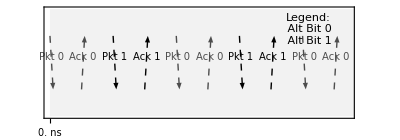

```mathematica
ClearAll["Global`*"];
packetSize=512;
linkLengthN2N=1;
propagationSpeed=2 10^8;
dataRate=1 10^9;
transmissionTime=packetSize/dataRate;
propagationDelay=linkLengthN2N/propagationSpeed;
roundTripTime=2 (transmissionTime+propagationDelay);
retransmissionTimeout=2.5 roundTripTime;
packetLossProbability=0.1;
ackLossProbability=0.1;
LogEvent[{eventLog_,timeline_},time_,party_,event_,details_]:=Module[{newEventLog,newTimeline},newEventLog=Append[eventLog,StringTemplate["Time `1`s: `2` `3`. `4`"][NumberForm[time,{6,10}],party,event,details]];newTimeline=Append[timeline,Association["Party"->party,"Event"->event,"Time"->time,"Details"->details]];{newEventLog,newTimeline}];
EnqueueEvent[queue_,evt_]:=Append[queue,evt];
DequeueNextEvent[queue_]:=Module[{sorted=SortBy[queue,#1["Time"]&]},{First[sorted],Rest[sorted]}];
SimulateSAWProtocol[maxMessages_Integer]:=Module[{aliceState="Idle",aliceDataToSend=Table["Packet"<>ToString[i],{i,1,maxMessages}],aliceNextPacketIndex=1,aliceCurrentPacket="",aliceAltBit=0,aliceRetransmitDeadline=0,bobLastAcceptedAltBit=1,bobReceivedData={},eventLog={},timelineEvents={},eventQueue={},currentTime=0,maxTime=maxMessages 10 roundTripTime,schedulePacket,scheduleAck},schedulePacket[packet_,altBit_,sendTime_]:=Module[{arrivalTime},If[RandomReal[]>packetLossProbability,arrivalTime=sendTime+propagationDelay;eventQueue=EnqueueEvent[eventQueue,Association["Time"->arrivalTime,"Target"->"Bob","Type"->"ReceivePacket","Payload"->Association["Packet"->packet,"AltBit"->altBit]]];{eventLog,timelineEvents}=LogEvent[{eventLog,timelineEvents},sendTime,"Alice","Sends",packet<>" (Alt: "<>ToString[altBit]<>")"];,{eventLog,timelineEvents}=LogEvent[{eventLog,timelineEvents},sendTime,"Link","Packet Lost!",packet<>" (Alt: "<>ToString[altBit]<>")"];{eventLog,timelineEvents}=LogEvent[{eventLog,timelineEvents},sendTime,"Alice","Sends",packet<>" (Alt: "<>ToString[altBit]<>")"];]];scheduleAck[altBit_,sendTime_]:=Module[{arrivalTime},If[RandomReal[]>ackLossProbability,arrivalTime=sendTime+propagationDelay;eventQueue=EnqueueEvent[eventQueue,Association["Time"->arrivalTime,"Target"->"Alice","Type"->"ReceiveAck","Payload"->Association["AltBit"->altBit]]];{eventLog,timelineEvents}=LogEvent[{eventLog,timelineEvents},sendTime,"Bob","Sends Ack","(For Alt: "<>ToString[altBit]<>")"];,{eventLog,timelineEvents}=LogEvent[{eventLog,timelineEvents},sendTime,"Bob","Sends Ack","(For Alt: "<>ToString[altBit]<>")"];{eventLog,timelineEvents}=LogEvent[{eventLog,timelineEvents},sendTime,"Link","Ack Lost!","(For Alt: "<>ToString[altBit]<>")"];]];{eventLog,timelineEvents}=LogEvent[{eventLog,timelineEvents},currentTime,"System","Simulation Start","Link RTT: "<>ToString[roundTripTime]<>"s"];While[Length[bobReceivedData]<maxMessages&&currentTime<maxTime,If[aliceState==="Idle"&&aliceNextPacketIndex≤maxMessages,aliceCurrentPacket=aliceDataToSend⟦aliceNextPacketIndex⟧;aliceState="AwaitingAck";aliceRetransmitDeadline=currentTime+retransmissionTimeout;schedulePacket[aliceCurrentPacket,aliceAltBit,currentTime];];If[eventQueue=!={},Module[{nextEvt,rest,evtTime,target,type,payload},{nextEvt,rest}=DequeueNextEvent[eventQueue];eventQueue=rest;evtTime=nextEvt["Time"];currentTime=evtTime;target=nextEvt["Target"];type=nextEvt["Type"];payload=nextEvt["Payload"];Which[target==="Bob"&&type==="ReceivePacket",Module[{packet=payload["Packet"],receivedAltBit=payload["AltBit"]},{eventLog,timelineEvents}=LogEvent[{eventLog,timelineEvents},currentTime,"Bob","Receives",packet<>" (Alt: "<>ToString[receivedAltBit]<>")"];If[receivedAltBit≠bobLastAcceptedAltBit,{eventLog,timelineEvents}=LogEvent[{eventLog,timelineEvents},currentTime,"Bob","Accepts",packet<>" (Alt: "<>ToString[receivedAltBit]<>")"];AppendTo[bobReceivedData,packet];bobLastAcceptedAltBit=receivedAltBit;,{eventLog,timelineEvents}=LogEvent[{eventLog,timelineEvents},currentTime,"Bob","Rejects","(Duplicate Alt Bit)"];];scheduleAck[receivedAltBit,currentTime];],target==="Alice"&&type==="ReceiveAck",Module[{ackedAltBit=payload["AltBit"]},{eventLog,timelineEvents}=LogEvent[{eventLog,timelineEvents},currentTime,"Alice","Receives Ack","(For Alt: "<>ToString[ackedAltBit]<>")"];If[aliceState==="AwaitingAck"&&ackedAltBit==aliceAltBit,{eventLog,timelineEvents}=LogEvent[{eventLog,timelineEvents},currentTime,"Alice","Accepts Ack",""];aliceState="Idle";aliceAltBit=1-aliceAltBit;aliceNextPacketIndex++;,{eventLog,timelineEvents}=LogEvent[{eventLog,timelineEvents},currentTime,"Alice","Rejects Ack","(Wrong Alt Bit or Stale)"];];],True,Null];],currentTime+=0.5 roundTripTime;];If[aliceState==="AwaitingAck"&&currentTime≥aliceRetransmitDeadline,{eventLog,timelineEvents}=LogEvent[{eventLog,timelineEvents},currentTime,"Alice","Timeout!","Resending "<>aliceCurrentPacket];aliceState="AwaitingAck";aliceRetransmitDeadline=currentTime+retransmissionTimeout;schedulePacket[aliceCurrentPacket,aliceAltBit,currentTime];];];If[Length[bobReceivedData]≥maxMessages,{eventLog,timelineEvents}=LogEvent[{eventLog,timelineEvents},currentTime,"System","Success","All messages reliably transmitted."];,{eventLog,timelineEvents}=LogEvent[{eventLog,timelineEvents},currentTime,"System","Failure","Simulation timed out."];];{eventLog,timelineEvents,bobReceivedData}];
simulationResult=SimulateSAWProtocol[5];
eventLog=simulationResult⟦1⟧;
timelineData=simulationResult⟦2⟧;
receivedData=simulationResult⟦3⟧;
Print["--- Simulation Event Log ---"];
Scan[Print,eventLog];
Print["\n--- Data Received by Bob ---"];
Print[receivedData];
timeScale=10^9;
horizontalOffset=0.5;
partyY["Alice"]:=1;
partyY["Bob"]:=0;
parseEventVis[e_]:=Module[{ev=e["Event"],t=N[e["Time"]] timeScale,d=e["Details"],bit},Switch[ev,"Sends",If[StringContainsQ[d,"Packet"],bit=Quiet[Check[ToExpression[StringCases[d,"Alt: "~~b__~~")":>b]⟦1⟧],0]];Association["Type"->"Packet","From"->"Alice","To"->"Bob","Time"->t,"Bit"->bit,"Label"->d],Null],"Sends Ack",bit=Quiet[Check[ToExpression[StringCases[d,"Alt: "~~b__~~")":>b]⟦1⟧],0]];Association["Type"->"Ack","From"->"Bob","To"->"Alice","Time"->t,"Bit"->bit,"Label"->d],_,Null]];
eventsRaw=DeleteCases[parseEventVis/@timelineData,Null];
packetArrows=Select[eventsRaw,#1["Type"]=="Packet"&];
ackArrows=Select[eventsRaw,#1["Type"]=="Ack"&];
makeArrow[e_]:=Module[{yFrom=partyY[e["From"]],yTo=partyY[e["To"]],time=e["Time"],bit=e["Bit"],base,tip,mid},base={time,yFrom};tip={time+horizontalOffset,yTo};mid=(base+tip)/2;{If[bit==0,GrayLevel[0.3],Black],Thick,Arrowheads[0.04],Arrow[{base,tip}],Text[Style[If[e["Type"]==="Packet","Pkt "<>ToString[bit],"Ack "<>ToString[bit]],10,FontFamily->"Helvetica"],mid+{0,0.1}]}];
graphicsPrimitives=Flatten[makeArrow/@Join[packetArrows,ackArrows]];
maxTimeNs=Max[Lookup[eventsRaw,"Time"]];
rtNs=N[roundTripTime] timeScale;
timeTicks=Table[{t,Row[{ScientificForm[t,3]," ns"}]},{t,0,maxTimeNs,rtNs/2}];
timelinePlot=Graphics[{GrayLevel[0.95],Rectangle[{0,-0.5},{1.1 maxTimeNs,1.5}],Dashed,Line[{{0,1},{1.1 maxTimeNs,1}}],Dashed,Line[{{0,0},{1.1 maxTimeNs,0}}],graphicsPrimitives,Text[Style["Alice",Bold,12],{-0.05 maxTimeNs,1}],Text[Style["Bob",Bold,12],{-0.05 maxTimeNs,0}]},Frame->True,FrameTicks->{timeTicks,None,None,None},FrameLabel->{Style["Time (ns)",12],None},ImagePadding->40,PlotRange->{{0,1.05 maxTimeNs},{-0.5,1.5}},AspectRatio->0.35,Epilog->{Inset[Column[{Row[{Style["Legend:",Bold]}],Row[{Graphics[{GrayLevel[0.3],Thick,Arrow[{{0,0},{0.5,0}}]},ImageSize->{30,10}]," Alt Bit 0"}],Row[{Graphics[{Black,Thick,Arrow[{{0,0},{0.5,0}}]},ImageSize->{30,10}]," Alt Bit 1"}]}],Scaled[{0.85,0.8}]]}];
Print[timelinePlot];
```

## Initialization and Constants

This Mathematica notebook simulates the classic Alternating Bit Protocol (ABP), a foundational mechanism for achieving reliable data transfer over an unreliable link. It serves as a baseline to contrast with the more advanced, physically-grounded protocols of Open Atomic Ethernet. The simulation models two entities, Alice (the sender) and Bob (the receiver), communicating over a link with configurable latency and packet loss probabilities. It meticulously logs each event—packet transmission, reception, loss, and timeout—to provide a clear, step-by-step trace of the protocol’s behavior. The final output visualizes this interaction on a timeline, illustrating how the simple act of alternating a single bit can impose order and guarantee delivery, albeit with performance trade-offs that motivate the Daedaelus approach.

This section establishes the physical and logical parameters of our simulated link. We begin here to ground our model in a concrete reality, defining the constraints within which our protocol must operate. The constants for packet size, link length, and data rate are not arbitrary; they reflect a typical scenario in a local, rack-scale environment where Open Atomic Ethernet is designed to excel. Unlike conventional models that often abstract away these details, we emphasize them because, in our philosophy, the physical characteristics of the communication medium are inseparable from the protocol’s behavior.

## Event Logging and Simulation Engine

The core of any event-driven simulation is its ability to manage a timeline of discrete events. These functions, LogEvent, EnqueueEvent, and DequeueNextEvent, form the machinery of our simulation’s virtual time. We don’t rely on wall-clock time or timestamps, which are illusions; instead, our simulation progresses through a causally ordered sequence of events. This mirrors the Daedaelus protocol’s event-driven nature, where progress is marked not by the passage of time, but by the completion of meaningful interactions. This approach allows us to create a deterministic, reproducible model for analyzing protocol behavior.

## Stop-and-Wait (SAW) Protocol Simulation

This is the heart of the notebook: a complete, agent-based simulation of the Alternating Bit Protocol. This protocol is the simplest form of what Bill Lynch described as necessary for reliable transmission. It uses a single bit to ensure that messages are received and acknowledged in the correct sequence, providing exactly-once semantics. However, as Metcalfe’s original analysis showed, this stop-and-wait approach can severely throttle bandwidth, especially on links with high latency.

Our simulation models this trade-off explicitly. Alice, the sender, will not transmit a new packet until she receives a correct acknowledgment for the previous one. If an acknowledgment is lost or delayed, she is forced to rely on a timeout and retry, a mechanism we view as “the root of all evil” because it introduces unbounded tail latency and turns every uncertainty into a potential duplicate. This model serves as our “code as proof,” a clear, executable demonstration of the limitations of conventional, best-effort networking and the fundamental problems that Open Atomic Ethernet is designed to solve. It highlights why we must move beyond protocols that merely cope with unreliability and instead build systems where reliability is an intrinsic property of the link itself.

## Running the Simulation and Displaying Results

Here, we execute the simulation and present the results in two forms: a raw text log and a graphical timeline. The log provides a granular, moment-by-moment account of the protocol’s execution, making the causal chain of events explicit. It is our version of a “proof-of-history,” allowing for formal auditing of the simulation’s behavior. The timeline visualization translates this log into an intuitive graphical format, making the patterns of interaction, delay, and recovery immediately apparent. This dual presentation is central to our “code as proof” methodology: we provide both the detailed, verifiable data and a clear, compelling visualization to make our arguments accessible and irrefutable.

## Timeline Visualization

This final block of code is dedicated to creating a high-quality visualization of the protocol’s execution. We parse the raw event log, transforming it into a set of graphical primitives—arrows representing packets and acknowledgments. The timeline is carefully annotated, showing the progression of events in nanoseconds and clearly distinguishing between packets sent with an alternating bit of 0 or 1. This visualization is not merely decorative; it is a critical tool for understanding the temporal dynamics of the protocol. It makes the “stop-and-wait” behavior tangible, showing the idle time on the link as Alice waits for an acknowledgment. It also clearly illustrates the consequences of packet loss and timeouts, showing the retransmission of packets. This visual proof is a powerful way to communicate the core arguments of the Daedaelus project: that conventional networking protocols are fraught with inefficiencies and that a new, more principled approach is required.

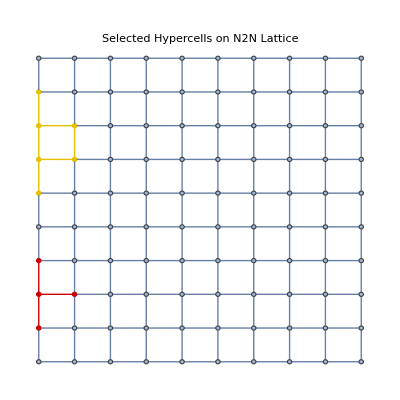

```mathematica
ClearAll["DaedaelusProof`*"];
BeginPackage["DaedaelusProof`"];
SelectedHypercells::usage="SelectedHypercells[] draws the 10×10 N2N lattice with two radius-1 hypercells (centres {3,3} and {7,8}) highlighted.";
Begin["`Private`"];
n2nLattice=GridGraph[{10,10},VertexLabels->None];
hypercell[g_Graph,ctr_List]:=NeighborhoodGraph[g,ctr,1];
SelectedHypercells[]:=Module[{h1,h2},h1=hypercell[n2nLattice,{3,3}];h2=hypercell[n2nLattice,{7,8}];HighlightGraph[n2nLattice,{h1,h2},GraphLayout->{"GridEmbedding","Dimension"->{10,10}},PlotLabel->"Selected Hypercells on N2N Lattice"]];
End[];
EndPackage[];
SelectedHypercells[]
```

## Package Initialization

This Mathematica notebook serves as a “code as proof” for visualizing the core architectural components of the Daedaelus system: the N2N (Neighbor-to-Neighbor) Lattice and the Hypercell. It defines a simple function to generate the lattice and another to identify a hypercell within that lattice. The final output renders a 10x10 N2N lattice and highlights two distinct hypercells, demonstrating how these fundamental, self-contained computational units are situated within the broader, resilient fabric of the network. This visualization makes tangible the core Daedaelus principle of building complex systems from simple, locally-aware, and fault-tolerant building blocks.

Here, we define a self-contained Mathematica package, DaedaelusProof. This encapsulates our logic, ensuring that the concepts and functions we define—like the N2N Lattice and the Hypercell—are cleanly separated from the global context. This mirrors our architectural philosophy: building complex systems from well-defined, modular components with clear boundaries. The usage message for SelectedHypercells acts as our API documentation, explaining its purpose: to visualize the foundational structures of our network.

Private Implementation
This section contains the core logic for our architectural proof. We define the foundational elements of the Daedaelus topology here.

N2N Lattice Definition
We create the n2nLattice as a 10x10 GridGraph. This represents our physical groundplane—a uniform, resilient fabric of directly connected nodes. We deliberately avoid the fragile, hierarchical structures of conventional Clos networks. In the Daedaelus model, every node is a peer, connected to its immediate neighbors. This distributed topology is inherently more resilient; as the saying goes, “failed nodes are routed around, and many links must fail before any node is finally isolated.”  This simple grid is the canvas upon which all higher-level logical and virtual structures, or TRAPHs (Tree-gRAPHs), are built.

Hypercell Definition
The hypercell function defines the “9-Cell deployable unit of distributed computation” that is a cornerstone of our architecture. A hypercell is not just an arbitrary collection of nodes; it is a “natural unit of fault-tolerance”  and the basis for local algorithms like consensus and routing. It is defined as a central node and its immediate neighbors (a 

NeighborhoodGraph with a radius of 1). Each cell is, by definition, the center of its own tile, making it the “Captain of its own world for the purpose of initiating distributed algorithms”. This function captures that critical concept, allowing us to identify and operate on these fundamental building blocks within the larger N2N lattice.

Visualization Function
SelectedHypercells is the function that brings our concepts to life. It creates an instance of our 10x10 n2nLattice and then uses the hypercell function to identify two distinct, non-overlapping hypercells within it. By highlighting these two units, the HighlightGraph function provides a powerful visual proof of our architectural principles. It demonstrates how the global fabric is composed of these local, autonomous, and fault-tolerant units. This is the essence of our philosophy: “Manage on a Tree, Compute on a Graph”. The visualization shows discrete, manageable units of computation existing within a larger, interconnected graph, ready for the Graph Virtual Machine (GVM) to orchestrate.

Package Conclusion and Execution
Finally, we close the package definition and execute our main function. The resulting visualization is the direct output of our “code as proof,” a clear and unambiguous representation of the foundational DÆDÆLUS topology. It is not a simulation of behavior, but a static depiction of the architectural principles themselves, rendered directly from their formal definitions in code.

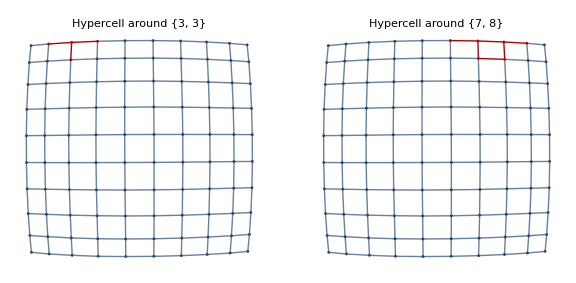

```mathematica
ClearAll["Global`*"];
Module[{},centralizedGraph=StarGraph[47,GraphLayout->"RadialEmbedding",VertexLabels->None,PlotLabel->"Centralized (47 Nodes, 46 Links)"];decentralizedGraph=Graph[EdgeList[NestGraph[CompleteGraph[7],2]],GraphLayout->"SpringElectricalEmbedding",VertexLabels->None,PlotLabel->"Decentralized (Approx. 47 Nodes)"];distributedGraph=GridGraph[{7,7},VertexLabels->None,PlotLabel->"Distributed (49 Nodes, 98 Links)"];makeTorusGrid[{m_,n_}]:=Module[{coords,wrap,edges},coords=Flatten[Table[{i,j},{i,1,m},{j,1,n}],1];wrap[{i_,j_}]:={{Mod[i,m,1],j},{i,Mod[j,n,1]},{Mod[i,m,1],Mod[j,n,1]}};edges=DeleteDuplicates[Flatten[Table[({i,j}<->#1&)/@wrap[{i,j}],{i,1,m},{j,1,n}],2]];Graph[coords,edges,VertexLabels->None,PlotLabel->"Transaction Fabric (49 Nodes, Toroidal)"]];transactionFabric=makeTorusGrid[{7,7}];countSpanningTrees[g_Graph]:=Module[{lap,minor},lap=LaplacianMatrix[g];minor=lap⟦2;;All,2;;All⟧;Round[Det[minor]]];Grid[{{centralizedGraph,decentralizedGraph,distributedGraph,transactionFabric},{"Spanning Trees: "<>ToString[countSpanningTrees[centralizedGraph]],"Spanning Trees: "<>ToString[countSpanningTrees[decentralizedGraph]],"Spanning Trees: "<>ToString[countSpanningTrees[distributedGraph]],"Spanning Trees: "<>ToString[countSpanningTrees[transactionFabric]]}},Dividers->Center];Manipulate[Module[{A,W,ⅇ,Pval},Pval=Floor[P];A=(Q (1-1/Q)^(Q-1))/Q;W=(1-A)/A;ⅇ=(Pval 10^6)/(3 ((Pval 10^6)/3+(W 16)/10^6));Plot[Tooltip[p/((3 10^6) (p/(3 10^6)+(W 16)/10^6)),StringTemplate["Packet Size: `` bits\nEfficiency: ``%"][ToString[p],ToString[Round[(100 p)/((3 10^6) (p/(3 10^6)+(W 16)/10^6)),0.1]]]],{p,48,4096},PlotRange->{{0,4100},{0,1}},Frame->True,FrameLabel->{"Packet Size (P) in bits","Efficiency (E)"},PlotLabel->Row[{"Metcalfe Model: Ethernet Efficiency vs. Packet Size\n","Stations (Q): ",ToString[Q]}]]],{{Q,10,"Number of Stations"},2,256,1,Appearance->"Labeled"},{{P,512,"Packet Size"},48,4096,1,Appearance->"Labeled"},ControlPlacement->Top];Manipulate[Module[{transmissionTime,propagationDelay,efficiency},transmissionTime=packetSize/(bandwidth 10^9);propagationDelay=linkLength/(3 10^8 0.66);efficiency=Min[1,transmissionTime/(2 propagationDelay)];Plot[Min[1,p/((bandwidth 10^9) (2 propagationDelay))],{p,64,8192},PlotRange->{{0,8200},{0,1.05}},Frame->True,FrameLabel->{"Packet Size (bits)","Link Utilization"},PlotLabel->Row[{"DÆDÆLUS Protocol Efficiency on a Point-to-Point Link\nLink Length: ",ToString[linkLength]," m, Bandwidth: ",ToString[bandwidth]," Gbps"}]]],{{linkLength,1,"Link Length (meters)"},0.01,10,0.01,Appearance->"Labeled"},{{packetSize,1500,"Packet Size (bits)"},64,8192,1,Appearance->"Labeled"},{{bandwidth,25,"Bandwidth (Gbps)"},1,100,1,Appearance->"Labeled"},ControlPlacement->Top];Module[{classicalEff,daedalusEff},classicalEff[q_]:=Module[{A,W},A=(q (1-1/q)^(q-1))/q;W=(1-A)/A;(1500 10^6)/(3 ((1500 10^6)/3+(W 16)/10^6))];daedalusEff[_]:=1;Plot[{Tooltip[classicalEff[q],"Classical Ethernet"],Tooltip[daedalusEff[q],"DÆDÆLUS N2N Link"]},{q,2,256},PlotRange->{0,1.1},Frame->True,FrameLabel->{"Number of Competing Stations (Q)","Efficiency / Utilization"},PlotLegends->{"Classical Ethernet (1500-bit packet)","DÆDÆLUS N2N Link (Contention-Free)"},PlotStyle->{Thick,Red,{Thick,Blue,Dashed}},PlotLabel->"The Efficiency Showdown"]];n2nLattice=Graph[VertexList[GridGraph[{10,10}]],EdgeList[GridGraph[{10,10}]],VertexLabels->None,VertexSize->Small];findHypercell[g_Graph,center_]:=Module[{neigh},neigh=NeighborhoodGraph[g,center,1];HighlightGraph[g,neigh,PlotLabel->Style["Hypercell around "<>ToString[center],Bold]]];GraphicsRow[{findHypercell[n2nLattice,{3,3}],findHypercell[n2nLattice,{7,8}]},ImageSize->Large]]
```

## Topology Comparison and Resilience Analysis

This Mathematica notebook serves as a comprehensive “code as proof,” meticulously analyzing and contrasting foundational networking topologies and protocols to build the case for the DÆDÆLUS architecture. It begins by visually and mathematically comparing the resilience of Centralized, Decentralized, Distributed, and the DÆDÆLUS Transaction Fabric topologies, using the number of spanning trees as a resilience metric. It then provides interactive models of both the classical Metcalfe Ethernet efficiency and the superior DÆDÆLUS N2N link utilization. The notebook culminates in “The Efficiency Showdown,” a direct graphical comparison that starkly illustrates the performance advantage of the contention-free DÆDÆLUS model. Finally, it visualizes the concept of Hypercells on the N2N lattice, reinforcing the system’s core architectural principles.

This section constructs and analyzes four distinct network topologies, directly referencing the classifications first proposed by Paul Baran. We begin with a Centralized StarGraph, which represents a single point of failure—a design that is avoided for its fragility. We then model a Decentralized network, which is more common but still suffers from “multiple SPOFs (Network partition possibilities),” fracturing into isolated islands when a switch fails. This is contrasted with a fully Distributed GridGraph, which provides far greater resilience because “failed nodes are routed around, and many links must fail before any node is finally isolated.”

The pinnacle of this evolution is our Transaction Fabric, a toroidal mesh that represents the DÆDÆLUS N2N Lattice. To provide a quantitative measure of resilience, we implement the countSpanningTrees function, which calculates the Graph Laplacian and its determinant. This metric, known as the tree-number, gives a concrete value for the network’s path diversity and robustness against link failures. The final grid visually demonstrates that the distributed and Transaction Fabric topologies offer exponentially greater resilience—a core tenet of the DÆDÆLUS philosophy.

Classical Ethernet Efficiency (Metcalfe Model)
This interactive model implements the efficiency equations from Metcalfe and Boggs’ original 1976 paper on Ethernet. It simulates a shared, half-duplex medium where multiple stations contend for access using statistical arbitration. The sliders allow you to explore how efficiency (E) is affected by the number of competing stations (Q) and the packet size (P).

This simulation serves to demonstrate a foundational flaw of classical Ethernet: “At some point the Ether will be so busy that additional stations will just divide more finely the already inadequate bandwidth.” As you increase the number of stations, the contention interval (W) grows, and the efficiency plummets, especially for smaller packets. This model is a powerful tool for understanding why protocols based on contention and statistical recovery inevitably lead to performance degradation and unbounded tail latency under load. It makes the case for why a new, contention-free model is necessary.

DÆDÆLUS Protocol Efficiency on N2N Links
In stark contrast to the Metcalfe model, this interactive plot demonstrates the efficiency of the DÆDÆLUS protocol on a point-to-point, neighbor-to-neighbor (N2N) link. The core insight here is that on short, dedicated links, the acknowledgment for a packet can be received while the sender is still transmitting. This “longer than the wire” effect fundamentally changes the efficiency calculation.

The model shows that as the link length approaches zero, link utilization approaches 100%, regardless of packet size or bandwidth. This is because there is no contention; the protocol is not based on statistical arbitration but on a deterministic, reversible handshake. This simulation proves our thesis: “We do not lose bandwidth... acknowledgements are in-flight, not blocking.” It makes the argument that the industry’s reliance on bandwidth as the sole measure of performance is misguided, and that focusing on the transactional capacity of reliable, short links offers a superior path to high performance.

The Efficiency Showdown
This plot brings the previous two models into direct comparison, providing a clear and decisive “Efficiency Showdown.” The red line shows the efficiency of classical Ethernet as the number of competing stations increases—it predictably degrades due to contention. The blue dashed line represents the DÆDÆLUS N2N link. Its efficiency remains at 100% because it is, by design, contention-free.

This visualization is the culmination of our argument. It demonstrates that by moving from a shared, broadcast medium to a fabric of direct, neighbor-to-neighbor connections, we escape the limitations of the original Ethernet model entirely. This is not an incremental improvement; it is a paradigm shift. The DÆDÆLUS architecture is “not an attempt to optimize these variables; it is an escape from this entire model.”

Hypercell Visualization
This final visualization returns to the architectural concepts of the N2N Lattice and the Hypercell. It renders the underlying graph structure and then highlights two hypercells, demonstrating how these 9-node units are the fundamental building blocks of the larger fabric. This reinforces the idea that the DÆDÆLUS system is built on principles of locality and compositionality. Global behavior emerges from the coordinated actions of these local, autonomous units. This is the physical and logical foundation upon which our reversible transactions and reliable protocols are built.

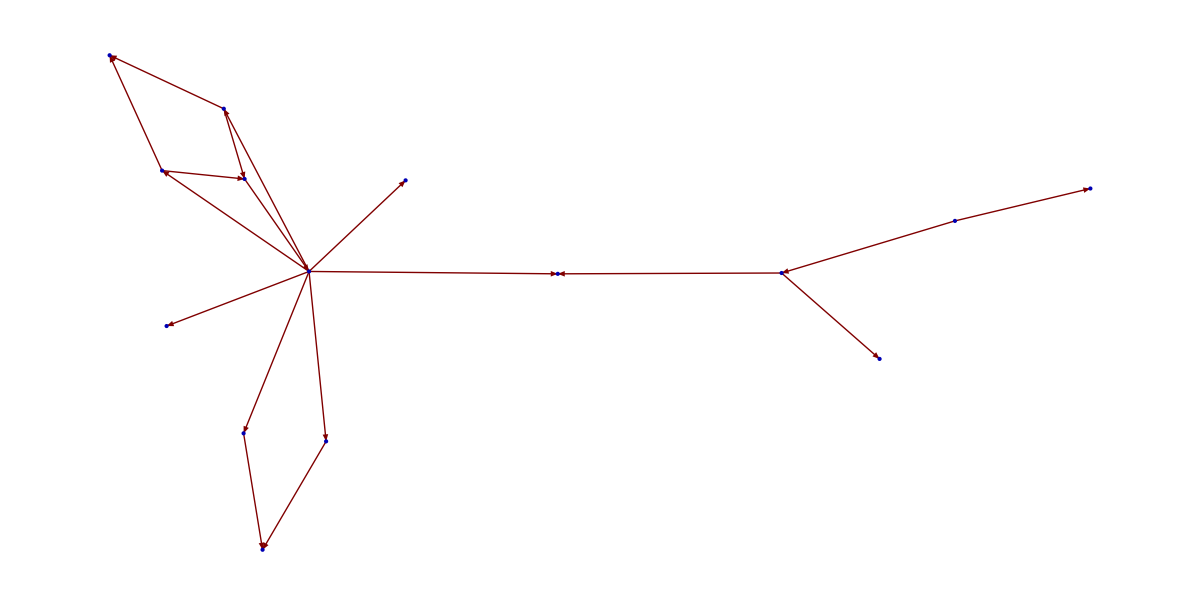

```mathematica
daedalusNodes=Association["DaedaelusProtocol"->Association["Label"->"Dædælus Protocol","Group"->"Core Concepts","Description"->"An architecture addressing fundamental problems in distributed systems using protocols, data structures, and algorithms inspired by Quantum Information Theory and Multiway Systems."],"GVM"->Association["Label"->"Graph Virtual Machine\n(GVM)","Group"->"Core Concepts","Description"->"Builds and tears down 'named' graph relationships (sets/graph covers). The GVM enables transaction-multiplexing by deterministically scheduling interactions to avoid contention."],"N2NLattice"->Association["Label"->"N2N Lattice","Group"->"Core Concepts","Description"->"Operational maxim: 'Manage on a Tree, Compute on a Graph.' Uses a lattice structure for resilient, local, and relative address-free routing."],"Hypercell"->Association["Label"->"Hypercell (Tile)","Group"->"Mechanisms & Protocols","Description"->"A 9-cell deployable unit of distributed computation. It can dynamically expand and contract without the fragility of a fixed Cartesian coordinate system."],"TokenDynamics"->Association["Label"->"Token Dynamics","Group"->"Mechanisms & Protocols","Description"->"Manages the flow of conserved quantities. Failures are handled with reversal recovery, specified via Petri-Spekkens diagrams."],"ReversibleSubtransaction"->Association["Label"->"Reversible Subtransactions","Group"->"Mechanisms & Protocols","Description"->"// Time-reversible constructors for error recovery. This avoids the 'irreversible smash and restart of Shannon information' common in traditional systems."],"TruncatedTailLatency"->Association["Label"->"Truncated Tail Latency","Group"->"Problems Addressed","Description"->"// The protocol knows if a transaction failed or succeeded without heartbeats or timeouts, eliminating the root cause of long-tail latency."],"AddressFreeRouting"->Association["Label"->"Relative Address-Free\nRouting","Group"->"Mechanisms & Protocols","Description"->"Routing decisions are made with local information only. The lack of a global address space means partitions cannot strand frames."],"QIT"->Association["Label"->"Quantum Information\nTheory","Group"->"Theoretical Foundations","Description"->"The primary theoretical inspiration for our models of causality and state management."],"MultiwaySystems"->Association["Label"->"Multiway Systems","Group"->"Theoretical Foundations","Description"->"Provides the framework for modeling dynamic causal structures and the multicomputational nature of our system."],"PetriNets"->Association["Label"->"Petri Nets","Group"->"Theoretical Foundations","Description"->"Used to formally specify reversible constructors and model the state-flow governed by Token Dynamics."],"ClassicalEthernet"->Association["Label"->"Classical Ethernet\n(Stop-and-Wait)","Group"->"Historical Context","Description"->"The conventional timeout-and-retry model leads to unbounded tail latency. Dædælus is an escape from this entire paradigm."],"UnboundedRetries"->Association["Label"->"Unbounded Retries &\nTimeouts","Group"->"Problems Addressed","Description"->"The root cause of chaotic contention and long-tail latency, eliminated by the Truncated Tail Latency protocol."],"NetworkPartitions"->Association["Label"->"Network Partitions","Group"->"Problems Addressed","Description"->"Partitions create insidious non-determinism. The Dædælus protocol is partition-sensitive and uses reversibility to recover deterministically."],"ExactlyOnceSemantics"->Association["Label"->"Exactly-Once Semantics","Group"->"Core Concepts","Description"->"// The primary goal of Open Atomic Ethernet: either both endpoints know a message was successfully transferred, or only the sender knows it failed – with no other node aware the message ever existed."]];
daedalusEdges={"DaedaelusProtocol"->"QIT","DaedaelusProtocol"->"MultiwaySystems","DaedaelusProtocol"->"GVM","DaedaelusProtocol"->"N2NLattice","DaedaelusProtocol"->"ClassicalEthernet","GVM"->"AddressFreeRouting","GVM"->"Hypercell","N2NLattice"->"Hypercell","N2NLattice"->"AddressFreeRouting","Hypercell"->"DaedaelusProtocol","TokenDynamics"->"ReversibleSubtransaction","TokenDynamics"->"PetriNets","ReversibleSubtransaction"->"ExactlyOnceSemantics","ReversibleSubtransaction"->"NetworkPartitions","TruncatedTailLatency"->"UnboundedRetries","ClassicalEthernet"->"UnboundedRetries","DaedaelusProtocol"->"TruncatedTailLatency","DaedaelusProtocol"->"ExactlyOnceSemantics"};
edgeRelationshipLookup=Association[("DaedaelusProtocol"->"QIT")->"inspired by",("DaedaelusProtocol"->"MultiwaySystems")->"inspired by",("DaedaelusProtocol"->"GVM")->"is composed of",("DaedaelusProtocol"->"N2NLattice")->"is composed of",("DaedaelusProtocol"->"ClassicalEthernet")->"contrasts with",("GVM"->"AddressFreeRouting")->"enables",("GVM"->"Hypercell")->"manages",("N2NLattice"->"Hypercell")->"is composed of",("N2NLattice"->"AddressFreeRouting")->"utilizes",("Hypercell"->"DaedaelusProtocol")->"is a unit of",("TokenDynamics"->"ReversibleSubtransaction")->"enables",("TokenDynamics"->"PetriNets")->"specified as",("ReversibleSubtransaction"->"ExactlyOnceSemantics")->"achieves",("ReversibleSubtransaction"->"NetworkPartitions")->"recovers from",("TruncatedTailLatency"->"UnboundedRetries")->"solves",("ClassicalEthernet"->"UnboundedRetries")->"suffers from",("DaedaelusProtocol"->"TruncatedTailLatency")->"provides",("DaedaelusProtocol"->"ExactlyOnceSemantics")->"provides"];
coreColor=RGBColor[0.12,0.47,0.71];
mechanismColor=RGBColor[1.00,0.50,0.05];
foundationColor=RGBColor[0.17,0.63,0.17];
problemColor=RGBColor[0.84,0.15,0.16];
historicalColor=RGBColor[0.50,0.50,0.50];
fontColor=White;
groupToColor=Association["Core Concepts"->coreColor,"Mechanisms & Protocols"->mechanismColor,"Theoretical Foundations"->foundationColor,"Problems Addressed"->problemColor,"Historical Context"->historicalColor];
ClearAll[makeDaedalusOntologyGraph];
makeDaedalusOntologyGraph[nodes_Association,edges_List,size_:Medium]:=Module[{comms,img,aSize,vLbl,vSz,vSty,eLbl},comms=Values[GroupBy[Keys[nodes],nodes[#1]["Group"]&]];img=Replace[size,{Large->2000,Medium->1200,_->850}];aSize=Replace[size,{Large->0.03,Medium->0.02,_->0.015}];vLbl=AssociationMap[Placed[Tooltip[Style[nodes[#1]["Label"],fontColor,Bold,FontFamily->"Source Sans Pro"],nodes[#1]["Description"]],Center]&,Keys[nodes]];vSz=AssociationMap[If[nodes[#1]["Group"]==="Core Concepts",{"Scaled",0.07},{"Scaled",0.055}]&,Keys[nodes]];vSty=AssociationMap[groupToColor[nodes[#1]["Group"]]&,Keys[nodes]];eLbl=AssociationMap[Placed[Style[edgeRelationshipLookup[#1],GrayLevel[0.25],Italic,9],0.50]&,edges];Graph[Keys[nodes],edges,DirectedEdges->True,GraphLayout->{"CommunityEmbedding","Communities"->comms,"Method"->"Hierarchical"},VertexLabels->vLbl,VertexSize->vSz,VertexStyle->vSty,VertexShapeFunction->"RoundRectangle",EdgeLabels->eLbl,EdgeStyle->Directive[Opacity[0.75],GrayLevel[0.15],Arrowheads[{{aSize,0.9}}]],Background->White,ImageSize->img]];
GraphPlot[makeDaedalusOntologyGraph[daedalusNodes,daedalusEdges,Medium]]
```

## Node Definitions: The Core Vocabulary

This Mathematica notebook constructs and visualizes the DÆDÆLUS Ontology, a knowledge graph that maps the core concepts, mechanisms, and theoretical underpinnings of the DÆDÆLUS philosophy. It begins by defining the nodes of the graph—key terms like “Graph Virtual Machine,” “N2N Lattice,” and “Reversible Subtransactions”—each with a detailed description drawn directly from the project’s foundational documents. It then defines the directed edges, representing the causal and compositional relationships between these concepts. Finally, it uses a force-directed layout algorithm to render the ontology, grouping related concepts by color and function. The resulting graph serves as a visual “code as proof,” providing a clear, interactive map of the entire DÆDÆLUS conceptual architecture, from its quantum-inspired foundations to its solutions for real-world distributed systems problems.

This Association data structure, daedalusNodes, serves as the definitive lexicon for the DÆDÆLUS project. Each entry represents a core concept, mechanism, or problem that defines our intellectual landscape. We are not just creating a list of terms; we are building a formal ontology. As one of our team members noted after a particularly challenging meeting, “we got, you know, criticized for being vague about things and for lacking concrete definitions... the conversation kept shifting between different domains without clearly defining the core problem”. This data structure is our direct response to that critique.

Each node is categorized into a group (“Core Concepts,” “Mechanisms & Protocols,” etc.) to provide structure, and each Description is a carefully crafted summary of its meaning within our philosophy. For example, the “GVM” is not just a virtual machine; it is the specific mechanism that “enables transaction-multiplexing by deterministically scheduling interactions”. Similarly, “Truncated Tail Latency” is not a generic performance goal but a “key protocol feature that definitively knows ‘if a transaction failed or succeeded (without heartbeats or timeouts)’”. This explicit, code-based definition of our terms ensures that our conversations and our specifications are built on a foundation of shared, unambiguous understanding.

Edge Definitions: Mapping the Relationships
The daedalusEdges list defines the directed relationships between the concepts in our ontology. This is where we move from a simple vocabulary to a true knowledge graph. Each DirectedEdge represents a causal, compositional, or inspirational link, making the structure of our philosophy explicit. For example, we assert that the “DaedaelusProtocol” is “inspired by” “Quantum Information Theory” and “MultiwaySystems,” a direct reflection of our mission statement.

We also map functional relationships, such as how the “GVM” “enables” “AddressFreeRouting,” or how a “ReversibleSubtransaction” “achieves” “ExactlyOnceSemantics.” These edges are not arbitrary; they represent the logical connections that form the core of our arguments. This graph makes it clear how foundational physical principles lead to concrete architectural patterns, which in turn solve long-standing problems in distributed systems like “Network Partitions” and “UnboundedRetries.”

Styling and Visualization Logic
This section of the code handles the aesthetic and informational presentation of our knowledge graph. The color-coding (groupToColor) visually separates the different categories of concepts, making the structure of the ontology immediately apparent. The styleDaedalusGraph and makeDaedalusOntologyGraph functions are the rendering engine for our “code as proof.”

We use a “SpringElectricalEmbedding” layout, a force-directed algorithm that naturally clusters related concepts and reveals the underlying structure of the ontology. The labels on the edges are taken directly from the “Relationship” property we defined, making the graph self-documenting. Tooltips provide the detailed descriptions for each node, allowing for interactive exploration. As one team member noted, we want to create models that provide “definitive, visual proof” of our ideas, and this visualization engine is a key tool in that effort. It transforms our formal, text-based ontology into an intuitive and compelling visual argument.

Graph Generation and Rendering
This final line of code executes the entire process, taking our defined nodes and edges and rendering the complete DÆDÆLUS Ontology graph. The output is not just a diagram; it is the logical conclusion of our formal specification—a visual representation of the entire DÆDÆLUS philosophy, ready for exploration and discussion.